Find a cycle and delete all its edges, but not its vertices.
Find all cycles between consecutive pairs of vertices.
Delete all internal edges, and treat the remaining cycle as an original.
Repeat.

An internal vertex is a vertex within the current cycle.

```mathematica
l2cycle[list_]:=Join[Table[list[[i]]<->list[[i+1]],{i,1,Length[list]-1}],{First[list]<->Last[list]}]
l2pairs[list_]:=Join[Table[{list[[i]],list[[i+1]]},{i,1,Length[list]-1}],{{First[list],Last[list]}}]
```

```mathematica
g1=CompleteGraph[4];
GraphPlot[%,VertexLabeling->True]
c1=First[FindCycle[g,∞,1]]
v1=Map[First,c1]
g2=Graph[Complement[EdgeList[g1],Map[Sort,c1]]]
c2=Map[l2cycle[FindShortestPath[g2,#[[1]],#[[2]]]]&,l2pairs[v1]]
v2=Complement[Map[First,Flatten[c2]],v1]
g3=Graph[Complement[EdgeList[g2],DeleteDuplicates[Map[Sort,Flatten[c2]]]]]
call=Join[c1,c2]
```

```mathematica
cygenset[g0_,maxsteps_]:=
Block[{g=g0,cs=FindCycle[g0,∞,1],allcy={},allg={}},
Block[{vs=Map[First,First[cs]],steps=1},
While[(EdgeCount[g]≠0)&&(steps≤maxsteps),
steps++;
g=Graph[Complement[EdgeList[g],DeleteDuplicates[Map[Sort,Flatten[cs]]]]];
allg=Append[allg,g];
(*Print[vs];
Print[cs];
Print[EdgeList[g]];*)
If[EdgeCount[g]>0&&Length[vs]>1&&VertexCount[g]>0,
cs=Map[l2cycle[FindShortestPath[g,#[[1]],#[[2]]]]&,l2pairs[vs]];
allcy=Join[allcy,cs];
(*Print[cs];
Print[allcy];
Print["hi"];*)
vs=Complement[Map[First,Flatten[cs]],vs],steps=maxsteps+1]];{allcy,allg}
]]
```

```mathematica
Monitor[Table[EdgeCount[Last[Last[cygenset[WheelGraph[i],1000]]]],{i,4,100}],i]
```

{0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0}

```mathematica
Table[Mod[i-1,10]+1,{i,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10}

```mathematica
Monitor[Table[EdgeCount[GraphUnion@@Map[Graph,First[cygenset[WheelGraph[i],1000]]]]-EdgeCount[WheelGraph[i]],{i,4,70}],i]
```

{0,0,0,1,2,2,2,3,4,4,4,5,6,6,6,7,8,8,8,9,10,10,10,11,12,12,12,13,14,14,14,15,16,16,16,17,18,18,18,19,20,20,20,21,22,22,22,23,24,24,24,25,26,26,26,27,28,28,28,29,30,30,30,31,32,32,32}

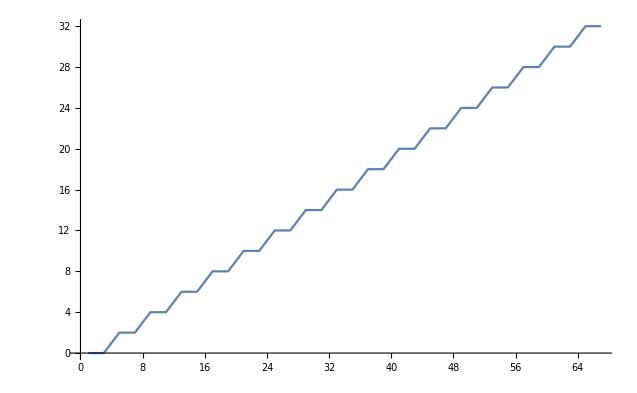

```mathematica
ListPlot[%,Joined->True]
```


{-Graphics-,-Graphics-,-Graphics-}

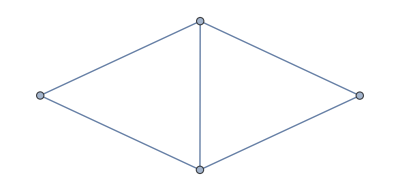
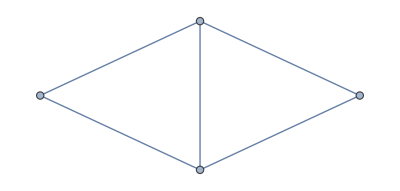
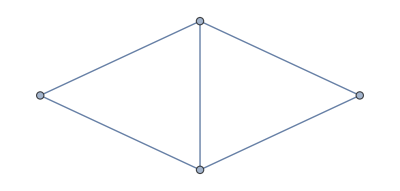

```mathematica
Map[Graph,{{1<->2,2<->4,1<->4},{4<->2,2<->3,4<->3},{1<->2,2<->3,1<->3}}]
Table[GraphUnion[%[[Mod[i-1,Length[%]]+1]],%[[Mod[i,Length[%]]+1]]],{i,1,Length[%]}]
```

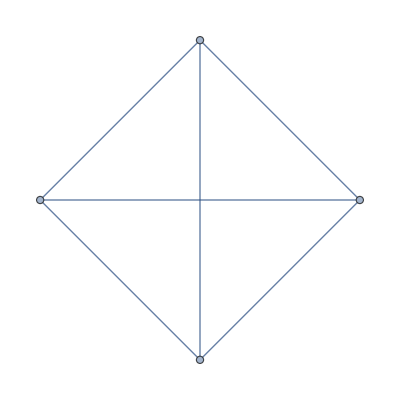

```mathematica
GraphUnion@@Map[Graph,{{1<->2,2<->4,1<->4},{4<->2,2<->3,4<->3},{1<->2,2<->3,1<->3}}]
```

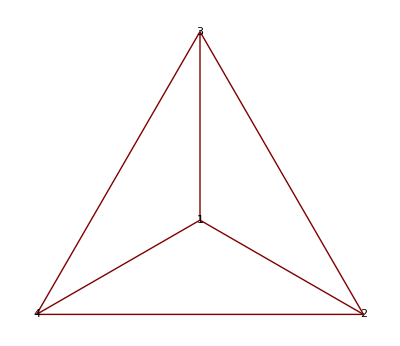

{1<->4,4<->3,3<->1}

{1,4,3}



{{1<->2,2<->4,1<->4},{4<->2,2<->3,4<->3},{1<->2,2<->3,1<->3}}

{2}

-Graphics-

{1<->4,4<->3,3<->1,{1<->2,2<->4,1<->4},{4<->2,2<->3,4<->3},{1<->2,2<->3,1<->3}}

```mathematica
g1=CompleteGraph[4];
GraphPlot[%,VertexLabeling->True]
c1=First[sofar=FindCycle[g,∞,1]]
v1=Map[First,c1]
g2=Graph[Complement[EdgeList[g1],Map[Sort,c1]]]
c2=Map[l2cycle[FindShortestPath[g2,#[[1]],#[[2]]]]&,l2pairs[v1]]
v2=Complement[Map[First,Flatten[c2]],v1]
g3=Graph[Complement[EdgeList[g2],DeleteDuplicates[Map[Sort,Flatten[c2]]]]]
call=Join[c1,c2]
```

-Graphics-

{1<->4,3<->4,1<->3}

{1,4,3}

{1<->2,2<->3,2<->4}

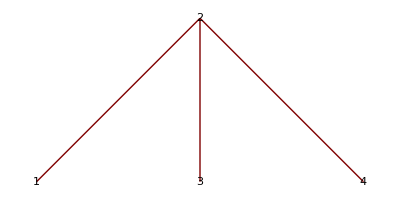

{1,2,4}

{2<->3,2<->4}

```mathematica
g=CompleteGraph[4];
GraphPlot[%,VertexLabeling->True]
c1=Map[Sort,First[sofar=FindCycle[g,∞,1]]]
Map[First,First[sofar=FindCycle[g,∞,1]]]
Complement[EdgeList[g],c1]
g2=Graph[%];
GraphPlot[%,VertexLabeling->True]
FindShortestPath[g2,1,4]
Complement[EdgeList[g2],{%[[1]]<->%[[2]]}]
```

```mathematica
gc2[n_]:=∑_(k=3)^n ((∏_(i=1)^k (i-k+n))/k)
```

```mathematica
gc2[8]
```

16036

```mathematica
Table[{n,(6.4000840435660844*10^-6*gc2[n]*2^n)/60},{n,5,15}]
```

{{5,0.00025259},{6,0.00268974},{7,0.0320038},{8,0.437895},{9,6.86105},{10,121.465},{11,2397.8},{12,52202.8},{13,1.24218×10^6},{14,3.20665×10^7},{15,8.92432×10^8}}

```mathematica
Length[EdgeList[CompleteGraph[10]]]
```

45

```mathematica
FindPeaks[{24.762,24.788,24.830,24.918,25.867,25.876,25.888,25.913,26.902,26.907,26.919,26.925,26.953,27.014,27.108,27.153,27.283,27.324,27.387,27.390,27.357,27.361,27.398,27.447,27.470,27.525,27.537,27.550}]
```

{{20,27.39},{28,27.55}}

```mathematica
Solve[27.55==c*16036*2^28]
```

{{c→6.40008×10^-12}}

```mathematica
4.0889142518974397*
```

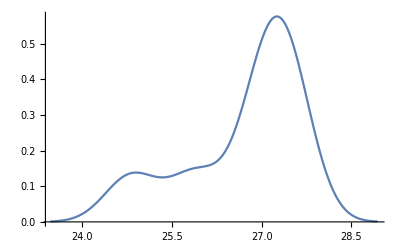

```mathematica
SmoothHistogram[{24.762,24.788,24.830,24.918,25.867,25.876,25.888,25.913,26.902,26.907,26.919,26.925,26.953,27.014,27.108,27.153,27.283,27.324,27.387,27.390,27.357,27.361,27.398,27.447,27.470,27.525,27.537,27.550}]
```

```mathematica
goodgraph[graph_]:=Block[{vd=And@@Map[#>2&,VertexDegree[graph]]},Piecewise[{{Block[{vc=VertexConnectivity[graph]},Piecewise[{{Block[{ec=EdgeConnectivity[graph]},Piecewise[{{Block[{cyd=Length[FindCycle[graph,∞,3]]},Piecewise[{{True, cyd==3}, {False, cyd≠3}}]], ec>1}, {False, ec≤1}}]], vc>1}, {False, vc≤1}}]], vd}, {False, ¬vd}}]]
```

```mathematica
Length[EdgeList[CompleteGraph[
```

```mathematica
gedges[graph_]:=Block[{ged=(Length[EdgeList[graph]]≤36)},Piecewise[{{goodgraph[graph], ged}, {False, ¬ged}}]]
```

```mathematica
lt45= Select[GraphData[;;45],gedges[GraphData[#]]&];
```

```mathematica
Length[lt45]
```

2022

```mathematica
lt45[[1]]
```

```mathematica
toH[name_,number_]:=StringJoin["graph_",ToString[number],"=(\"",ToString[name],"\",",StringReplace[ToString[Sort[Map[Sort,Map[{#[[1]]-1,#[[2]]-1}&,EdgeList[GraphData[name]]]]]],{"{"->"[","}"->"]"," "->""}],")\n"]
toH[{6,114},1]
```

graph_1=("{6, 114}",[[0,3],[0,4],[0,5],[1,3],[1,4],[1,5],[2,3],[2,4],[2,5],[3,5]])

```mathematica
AllToH[glist_]:=StringJoin["module GList where\n\n",StringJoin["gListLen = ", ToString[Length[glist]],"\n\n"],StringJoin["gList = [graph_0",Table[StringJoin[",graph_",ToString[i-1]],{i,2,Length[glist]}],"]\n\n"],Table[toH[glist[[i]],i-1],{i,1,Length[glist]}]]
AllToH[Take[lt45,3]]
```

module GList where

gListLen = 3

gList = [graph_0,graph_1,graph_2]

graph_0=("{6, 114}",[[0,3],[0,4],[0,5],[1,3],[1,4],[1,5],[2,3],[2,4],[2,5],[3,5]])
graph_1=("{6, 130}",[[0,2],[0,4],[0,5],[1,3],[1,4],[1,5],[2,4],[2,5],[3,4],[3,5]])
graph_2=("{6, 148}",[[0,2],[0,3],[0,4],[0,5],[1,3],[1,4],[1,5],[2,3],[2,4],[2,5],[3,4],[3,5],[4,5]])

```mathematica
Export["GList.hs",AllToH[lt45],"TEXT"]
```

GList.hs

```mathematica
Monitor[Table[{Length[EdgeList[GraphData[lt36[[d]]]]],Length[VertexList[GraphData[lt36[[d]]]]],EdgeConnectivity[GraphData[lt36[[d]]]],VertexConnectivity[GraphData[lt36[[d]]]],lt36[[d]]},{d,1,2022}],d]
```

{{10,6,3,3,{6,114}},{10,6,3,2,{6,130}},{13,6,3,3,{6,148}},{11,6,3,3,{6,149}},{13,7,3,3,{7,344}},{12,7,3,2,{7,550}},{13,7,3,2,{7,551}},{13,7,3,2,{7,552}},{14,7,3,2,{7,553}},{12,7,3,3,{7,737}},{13,7,3,3,{7,738}},{14,7,3,3,{7,740}},{12,7,3,3,{7,763}},{13,7,3,3,{7,764}},{13,7,3,3,{7,765}},{13,7,3,3,{7,766}},1990,{8,5,3,3,{Wheel,5}},{10,6,3,3,{Wheel,6}},{12,7,3,3,{Wheel,7}},{14,8,3,3,{Wheel,8}},{16,9,3,3,{Wheel,9}},{18,10,3,3,{Wheel,10}},{20,11,3,3,{Wheel,11}},{22,12,3,3,{Wheel,12}},{24,13,3,3,{Wheel,13}},{26,14,3,3,{Wheel,14}},{28,15,3,3,{Wheel,15}},{30,16,3,3,{Wheel,16}},{32,17,3,3,{Wheel,17}},{34,18,3,3,{Wheel,18}},{36,19,3,3,{Wheel,19}},{28,12,4,4,{WhiteBishop,{5,5}}}}
 |  |  |  |

```mathematica
comp[a_,b_]:=Block[{eless=(a[[1]]≤b[[1]])},Piecewise[{{True, ¬eless}, {Block[{vless=(a[[2]]<b[[2]])},Piecewise[{{True, vless}, {Block[{ecl=(a[[3]]<b[[3]])},Piecewise[{{True, ecl}, {False, ¬ecl}}]], ¬vless}}]], eless}}]]
```

```mathematica
comp[a_,b_]:=Piecewise[{{True, a[[1]]<b[[1]]}, {Piecewise[{{True, a[[3]]<b[[3]]}, {Piecewise[{{True, a[[2]]<b[[2]]}, {Piecewise[{{True, a[[4]]≤b[[4]]}, {False, a[[4]]>b[[4]]}}], a[[2]]==b[[2]]}, {False, a[[2]]>b[[2]]}}], a[[3]]==b[[3]]}, {False, a[[3]]>b[[3]]}}], a[[1]]==b[[1]]}, {False, a[[1]]>b[[1]]}}]
```

```mathematica
sorted=Sort[Out[4],comp[#1,#2]&];
```

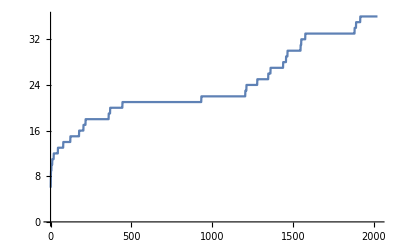

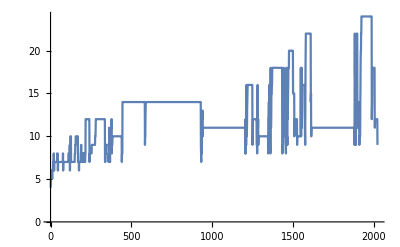

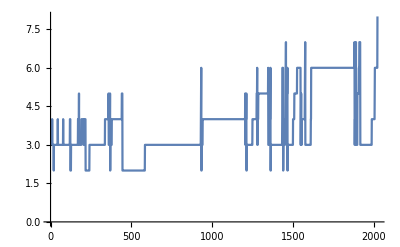

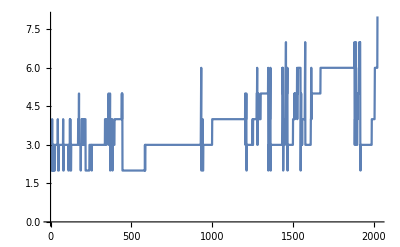

```mathematica
ListPlot[Map[#[[1]]&,sorted],Joined->True]
ListPlot[Map[#[[2]]&,sorted],Joined->True]
ListPlot[Map[#[[3]]&,sorted],Joined->True]
ListPlot[Map[#[[4]]&,sorted],Joined->True]
```

```mathematica
nsorted = Map[#[[5]]&,sorted];
```

```mathematica
nsorted[0]
```

{TetrahedralGraph,{Wheel,5},{JohnsonSkeleton,12},{Prism,3},UtilityGraph,{6,130},{6,114},{Hexahedral,3},{Wheel,6},PentatopeGraph,{King,{2,3}},{6,149},{Fan,{2,4}},{Fan,{3,3}},{Hexahedral,4},MoserSpindle,{Harary,{3,7}},{Heptahedral,2},{Heptahedral,7},1985,{Cone,{9,3}},{Cone,{6,5}},{Circulant,{12,{1,2,3}}},{Circulant,{12,{1,2,4}}},{Circulant,{12,{1,2,5}}},{Circulant,{12,{1,3,4}}},{Circulant,{12,{1,4,5}}},{Circulant,{12,{2,3,4}}},{CompleteBipartite,{6,6}},{Lattice,{2,6}},{Sextic,{12,1}},{Sextic,{12,2}},{Sextic,{12,3}},{VertexTransitive,{12,40}},{VertexTransitive,{12,45}},{VertexTransitive,{12,47}},{VertexTransitive,{12,48}},{Complete,9}}[0]
 |  |  |  |

```mathematica
topyindex[nsorted]
Export["pymainforcy3.txt",topy[nsorted]]
```

graph_1_4,graph_2_5,graph_3_5,graph_4_6,graph_5_6,graph_6_6,graph_7_6,graph_8_6,graph_9_6,graph_10_5,graph_11_6,graph_12_6,graph_13_6,graph_14_6,graph_15_6,graph_16_7,graph_17_7,graph_18_7,graph_19_7,graph_20_8,graph_21_6,graph_22_6,graph_23_6,graph_24_7,graph_25_7,graph_26_7,graph_27_7,graph_28_7,graph_29_7,graph_30_7,graph_31_7,graph_32_7,graph_33_7,graph_34_7,graph_35_7,graph_36_7,graph_37_7,graph_38_7,graph_39_7,graph_40_7,graph_41_8,graph_42_8,graph_43_8,graph_44_8,graph_45_6,graph_46_6,graph_47_7,graph_48_7,graph_49_7,graph_50_7,graph_51_7,graph_52_7,graph_53_7,graph_54_7,graph_55_7,graph_56_7,graph_57_7,graph_58_7,graph_59_7,graph_60_7,graph_61_7,graph_62_7,graph_63_7,graph_64_7,graph_65_7,graph_66_7,graph_67_7,graph_68_7,graph_69_7,graph_70_7,graph_71_7,graph_72_7,graph_73_7,graph_74_7,graph_75_7,graph_76_7,graph_77_8,graph_78_6,graph_79_7,graph_80_7,graph_81_7,graph_82_7,graph_83_7,graph_84_7,graph_85_7,graph_86_7,graph_87_7,graph_88_7,graph_89_7,graph_90_7,graph_91_7,graph_92_7,graph_93_7,graph_94_7,graph_95_7,graph_96_7,graph_97_7,graph_98_7,graph_99_7,graph_100_7,graph_101_7,graph_102_7,graph_103_7,graph_104_7,graph_105_7,graph_106_7,graph_107_7,graph_108_7,graph_109_7,graph_110_7,graph_111_8,graph_112_8,graph_113_8,graph_114_8,graph_115_8,graph_116_8,graph_117_8,graph_118_8,graph_119_9,graph_120_6,graph_121_7,graph_122_7,graph_123_10,graph_124_10,graph_125_10,graph_126_10,graph_127_7,graph_128_7,graph_129_7,graph_130_7,graph_131_7,graph_132_7,graph_133_7,graph_134_7,graph_135_7,graph_136_7,graph_137_7,graph_138_7,graph_139_7,graph_140_7,graph_141_7,graph_142_7,graph_143_7,graph_144_7,graph_145_7,graph_146_7,graph_147_7,graph_148_7,graph_149_7,graph_150_8,graph_151_8,graph_152_8,graph_153_9,graph_154_9,graph_155_9,graph_156_10,graph_157_10,graph_158_10,graph_159_10,graph_160_10,graph_161_10,graph_162_10,graph_163_10,graph_164_10,graph_165_10,graph_166_10,graph_167_10,graph_168_10,graph_169_10,graph_170_7,graph_171_7,graph_172_7,graph_173_7,graph_174_7,graph_175_7,graph_176_6,graph_177_7,graph_178_7,graph_179_7,graph_180_7,graph_181_7,graph_182_7,graph_183_7,graph_184_7,graph_185_7,graph_186_7,graph_187_8,graph_188_8,graph_189_9,graph_190_9,graph_191_7,graph_192_7,graph_193_7,graph_194_7,graph_195_7,graph_196_7,graph_197_7,graph_198_8,graph_199_8,graph_200_8,graph_201_8,graph_202_8,graph_203_8,graph_204_7,graph_205_7,graph_206_7,graph_207_8,graph_208_8,graph_209_7,graph_210_7,graph_211_7,graph_212_7,graph_213_7,graph_214_7,graph_215_8,graph_216_8,graph_217_12,graph_218_12,graph_219_12,graph_220_12,graph_221_12,graph_222_12,graph_223_12,graph_224_12,graph_225_12,graph_226_12,graph_227_12,graph_228_12,graph_229_12,graph_230_12,graph_231_12,graph_232_12,graph_233_12,graph_234_12,graph_235_12,graph_236_12,graph_237_12,graph_238_12,graph_239_12,graph_240_12,graph_241_7,graph_242_8,graph_243_8,graph_244_8,graph_245_8,graph_246_8,graph_247_8,graph_248_8,graph_249_8,graph_250_8,graph_251_8,graph_252_8,graph_253_8,graph_254_8,graph_255_9,graph_256_9,graph_257_9,graph_258_9,graph_259_9,graph_260_9,graph_261_9,graph_262_9,graph_263_9,graph_264_9,graph_265_9,graph_266_9,graph_267_9,graph_268_9,graph_269_9,graph_270_9,graph_271_9,graph_272_9,graph_273_9,graph_274_9,graph_275_9,graph_276_10,graph_277_10,graph_278_10,graph_279_11,graph_280_12,graph_281_12,graph_282_12,graph_283_12,graph_284_12,graph_285_12,graph_286_12,graph_287_12,graph_288_12,graph_289_12,graph_290_12,graph_291_12,graph_292_12,graph_293_12,graph_294_12,graph_295_12,graph_296_12,graph_297_12,graph_298_12,graph_299_12,graph_300_12,graph_301_12,graph_302_12,graph_303_12,graph_304_12,graph_305_12,graph_306_12,graph_307_12,graph_308_12,graph_309_12,graph_310_12,graph_311_12,graph_312_12,graph_313_12,graph_314_12,graph_315_12,graph_316_12,graph_317_12,graph_318_12,graph_319_12,graph_320_12,graph_321_12,graph_322_12,graph_323_12,graph_324_12,graph_325_12,graph_326_12,graph_327_12,graph_328_12,graph_329_12,graph_330_12,graph_331_12,graph_332_12,graph_333_12,graph_334_12,graph_335_12,graph_336_12,graph_337_7,graph_338_7,graph_339_7,graph_340_8,graph_341_8,graph_342_8,graph_343_9,graph_344_9,graph_345_9,graph_346_9,graph_347_9,graph_348_9,graph_349_9,graph_350_9,graph_351_9,graph_352_9,graph_353_9,graph_354_9,graph_355_9,graph_356_9,graph_357_9,graph_358_9,graph_359_7,graph_360_8,graph_361_8,graph_362_8,graph_363_11,graph_364_7,graph_365_8,graph_366_8,graph_367_8,graph_368_7,graph_369_10,graph_370_9,graph_371_9,graph_372_10,graph_373_10,graph_374_11,graph_375_11,graph_376_11,graph_377_12,graph_378_12,graph_379_8,graph_380_9,graph_381_9,graph_382_9,graph_383_10,graph_384_10,graph_385_10,graph_386_10,graph_387_10,graph_388_10,graph_389_10,graph_390_10,graph_391_10,graph_392_10,graph_393_10,graph_394_10,graph_395_10,graph_396_10,graph_397_10,graph_398_10,graph_399_10,graph_400_10,graph_401_10,graph_402_10,graph_403_10,graph_404_10,graph_405_10,graph_406_10,graph_407_10,graph_408_10,graph_409_10,graph_410_10,graph_411_10,graph_412_10,graph_413_10,graph_414_10,graph_415_10,graph_416_10,graph_417_10,graph_418_10,graph_419_10,graph_420_10,graph_421_10,graph_422_10,graph_423_10,graph_424_10,graph_425_10,graph_426_10,graph_427_10,graph_428_10,graph_429_10,graph_430_10,graph_431_10,graph_432_10,graph_433_10,graph_434_10,graph_435_10,graph_436_10,graph_437_10,graph_438_10,graph_439_10,graph_440_10,graph_441_7,graph_442_8,graph_443_8,graph_444_8,graph_445_14,graph_446_14,graph_447_14,graph_448_14,graph_449_14,graph_450_14,graph_451_14,graph_452_14,graph_453_14,graph_454_14,graph_455_14,graph_456_14,graph_457_14,graph_458_14,graph_459_14,graph_460_14,graph_461_14,graph_462_14,graph_463_14,graph_464_14,graph_465_14,graph_466_14,graph_467_14,graph_468_14,graph_469_14,graph_470_14,graph_471_14,graph_472_14,graph_473_14,graph_474_14,graph_475_14,graph_476_14,graph_477_14,graph_478_14,graph_479_14,graph_480_14,graph_481_14,graph_482_14,graph_483_14,graph_484_14,graph_485_14,graph_486_14,graph_487_14,graph_488_14,graph_489_14,graph_490_14,graph_491_14,graph_492_14,graph_493_14,graph_494_14,graph_495_14,graph_496_14,graph_497_14,graph_498_14,graph_499_14,graph_500_14,graph_501_14,graph_502_14,graph_503_14,graph_504_14,graph_505_14,graph_506_14,graph_507_14,graph_508_14,graph_509_14,graph_510_14,graph_511_14,graph_512_14,graph_513_14,graph_514_14,graph_515_14,graph_516_14,graph_517_14,graph_518_14,graph_519_14,graph_520_14,graph_521_14,graph_522_14,graph_523_14,graph_524_14,graph_525_14,graph_526_14,graph_527_14,graph_528_14,graph_529_14,graph_530_14,graph_531_14,graph_532_14,graph_533_14,graph_534_14,graph_535_14,graph_536_14,graph_537_14,graph_538_14,graph_539_14,graph_540_14,graph_541_14,graph_542_14,graph_543_14,graph_544_14,graph_545_14,graph_546_14,graph_547_14,graph_548_14,graph_549_14,graph_550_14,graph_551_14,graph_552_14,graph_553_14,graph_554_14,graph_555_14,graph_556_14,graph_557_14,graph_558_14,graph_559_14,graph_560_14,graph_561_14,graph_562_14,graph_563_14,graph_564_14,graph_565_14,graph_566_14,graph_567_14,graph_568_14,graph_569_14,graph_570_14,graph_571_14,graph_572_14,graph_573_14,graph_574_14,graph_575_14,graph_576_14,graph_577_14,graph_578_14,graph_579_14,graph_580_14,graph_581_14,graph_582_14,graph_583_14,graph_584_9,graph_585_10,graph_586_10,graph_587_12,graph_588_13,graph_589_14,graph_590_14,graph_591_14,graph_592_14,graph_593_14,graph_594_14,graph_595_14,graph_596_14,graph_597_14,graph_598_14,graph_599_14,graph_600_14,graph_601_14,graph_602_14,graph_603_14,graph_604_14,graph_605_14,graph_606_14,graph_607_14,graph_608_14,graph_609_14,graph_610_14,graph_611_14,graph_612_14,graph_613_14,graph_614_14,graph_615_14,graph_616_14,graph_617_14,graph_618_14,graph_619_14,graph_620_14,graph_621_14,graph_622_14,graph_623_14,graph_624_14,graph_625_14,graph_626_14,graph_627_14,graph_628_14,graph_629_14,graph_630_14,graph_631_14,graph_632_14,graph_633_14,graph_634_14,graph_635_14,graph_636_14,graph_637_14,graph_638_14,graph_639_14,graph_640_14,graph_641_14,graph_642_14,graph_643_14,graph_644_14,graph_645_14,graph_646_14,graph_647_14,graph_648_14,graph_649_14,graph_650_14,graph_651_14,graph_652_14,graph_653_14,graph_654_14,graph_655_14,graph_656_14,graph_657_14,graph_658_14,graph_659_14,graph_660_14,graph_661_14,graph_662_14,graph_663_14,graph_664_14,graph_665_14,graph_666_14,graph_667_14,graph_668_14,graph_669_14,graph_670_14,graph_671_14,graph_672_14,graph_673_14,graph_674_14,graph_675_14,graph_676_14,graph_677_14,graph_678_14,graph_679_14,graph_680_14,graph_681_14,graph_682_14,graph_683_14,graph_684_14,graph_685_14,graph_686_14,graph_687_14,graph_688_14,graph_689_14,graph_690_14,graph_691_14,graph_692_14,graph_693_14,graph_694_14,graph_695_14,graph_696_14,graph_697_14,graph_698_14,graph_699_14,graph_700_14,graph_701_14,graph_702_14,graph_703_14,graph_704_14,graph_705_14,graph_706_14,graph_707_14,graph_708_14,graph_709_14,graph_710_14,graph_711_14,graph_712_14,graph_713_14,graph_714_14,graph_715_14,graph_716_14,graph_717_14,graph_718_14,graph_719_14,graph_720_14,graph_721_14,graph_722_14,graph_723_14,graph_724_14,graph_725_14,graph_726_14,graph_727_14,graph_728_14,graph_729_14,graph_730_14,graph_731_14,graph_732_14,graph_733_14,graph_734_14,graph_735_14,graph_736_14,graph_737_14,graph_738_14,graph_739_14,graph_740_14,graph_741_14,graph_742_14,graph_743_14,graph_744_14,graph_745_14,graph_746_14,graph_747_14,graph_748_14,graph_749_14,graph_750_14,graph_751_14,graph_752_14,graph_753_14,graph_754_14,graph_755_14,graph_756_14,graph_757_14,graph_758_14,graph_759_14,graph_760_14,graph_761_14,graph_762_14,graph_763_14,graph_764_14,graph_765_14,graph_766_14,graph_767_14,graph_768_14,graph_769_14,graph_770_14,graph_771_14,graph_772_14,graph_773_14,graph_774_14,graph_775_14,graph_776_14,graph_777_14,graph_778_14,graph_779_14,graph_780_14,graph_781_14,graph_782_14,graph_783_14,graph_784_14,graph_785_14,graph_786_14,graph_787_14,graph_788_14,graph_789_14,graph_790_14,graph_791_14,graph_792_14,graph_793_14,graph_794_14,graph_795_14,graph_796_14,graph_797_14,graph_798_14,graph_799_14,graph_800_14,graph_801_14,graph_802_14,graph_803_14,graph_804_14,graph_805_14,graph_806_14,graph_807_14,graph_808_14,graph_809_14,graph_810_14,graph_811_14,graph_812_14,graph_813_14,graph_814_14,graph_815_14,graph_816_14,graph_817_14,graph_818_14,graph_819_14,graph_820_14,graph_821_14,graph_822_14,graph_823_14,graph_824_14,graph_825_14,graph_826_14,graph_827_14,graph_828_14,graph_829_14,graph_830_14,graph_831_14,graph_832_14,graph_833_14,graph_834_14,graph_835_14,graph_836_14,graph_837_14,graph_838_14,graph_839_14,graph_840_14,graph_841_14,graph_842_14,graph_843_14,graph_844_14,graph_845_14,graph_846_14,graph_847_14,graph_848_14,graph_849_14,graph_850_14,graph_851_14,graph_852_14,graph_853_14,graph_854_14,graph_855_14,graph_856_14,graph_857_14,graph_858_14,graph_859_14,graph_860_14,graph_861_14,graph_862_14,graph_863_14,graph_864_14,graph_865_14,graph_866_14,graph_867_14,graph_868_14,graph_869_14,graph_870_14,graph_871_14,graph_872_14,graph_873_14,graph_874_14,graph_875_14,graph_876_14,graph_877_14,graph_878_14,graph_879_14,graph_880_14,graph_881_14,graph_882_14,graph_883_14,graph_884_14,graph_885_14,graph_886_14,graph_887_14,graph_888_14,graph_889_14,graph_890_14,graph_891_14,graph_892_14,graph_893_14,graph_894_14,graph_895_14,graph_896_14,graph_897_14,graph_898_14,graph_899_14,graph_900_14,graph_901_14,graph_902_14,graph_903_14,graph_904_14,graph_905_14,graph_906_14,graph_907_14,graph_908_14,graph_909_14,graph_910_14,graph_911_14,graph_912_14,graph_913_14,graph_914_14,graph_915_14,graph_916_14,graph_917_14,graph_918_14,graph_919_14,graph_920_14,graph_921_14,graph_922_14,graph_923_14,graph_924_14,graph_925_14,graph_926_14,graph_927_14,graph_928_14,graph_929_14,graph_930_9,graph_931_8,graph_932_7,graph_933_11,graph_934_11,graph_935_8,graph_936_8,graph_937_12,graph_938_12,graph_939_12,graph_940_13,graph_941_10,graph_942_11,graph_943_11,graph_944_11,graph_945_11,graph_946_11,graph_947_11,graph_948_11,graph_949_11,graph_950_11,graph_951_11,graph_952_11,graph_953_11,graph_954_11,graph_955_11,graph_956_11,graph_957_11,graph_958_11,graph_959_11,graph_960_11,graph_961_11,graph_962_11,graph_963_11,graph_964_11,graph_965_11,graph_966_11,graph_967_11,graph_968_11,graph_969_11,graph_970_11,graph_971_11,graph_972_11,graph_973_11,graph_974_11,graph_975_11,graph_976_11,graph_977_11,graph_978_11,graph_979_11,graph_980_11,graph_981_11,graph_982_11,graph_983_11,graph_984_11,graph_985_11,graph_986_11,graph_987_11,graph_988_11,graph_989_11,graph_990_11,graph_991_11,graph_992_11,graph_993_11,graph_994_11,graph_995_11,graph_996_11,graph_997_11,graph_998_11,graph_999_11,graph_1000_11,graph_1001_11,graph_1002_11,graph_1003_11,graph_1004_11,graph_1005_11,graph_1006_11,graph_1007_11,graph_1008_11,graph_1009_11,graph_1010_11,graph_1011_11,graph_1012_11,graph_1013_11,graph_1014_11,graph_1015_11,graph_1016_11,graph_1017_11,graph_1018_11,graph_1019_11,graph_1020_11,graph_1021_11,graph_1022_11,graph_1023_11,graph_1024_11,graph_1025_11,graph_1026_11,graph_1027_11,graph_1028_11,graph_1029_11,graph_1030_11,graph_1031_11,graph_1032_11,graph_1033_11,graph_1034_11,graph_1035_11,graph_1036_11,graph_1037_11,graph_1038_11,graph_1039_11,graph_1040_11,graph_1041_11,graph_1042_11,graph_1043_11,graph_1044_11,graph_1045_11,graph_1046_11,graph_1047_11,graph_1048_11,graph_1049_11,graph_1050_11,graph_1051_11,graph_1052_11,graph_1053_11,graph_1054_11,graph_1055_11,graph_1056_11,graph_1057_11,graph_1058_11,graph_1059_11,graph_1060_11,graph_1061_11,graph_1062_11,graph_1063_11,graph_1064_11,graph_1065_11,graph_1066_11,graph_1067_11,graph_1068_11,graph_1069_11,graph_1070_11,graph_1071_11,graph_1072_11,graph_1073_11,graph_1074_11,graph_1075_11,graph_1076_11,graph_1077_11,graph_1078_11,graph_1079_11,graph_1080_11,graph_1081_11,graph_1082_11,graph_1083_11,graph_1084_11,graph_1085_11,graph_1086_11,graph_1087_11,graph_1088_11,graph_1089_11,graph_1090_11,graph_1091_11,graph_1092_11,graph_1093_11,graph_1094_11,graph_1095_11,graph_1096_11,graph_1097_11,graph_1098_11,graph_1099_11,graph_1100_11,graph_1101_11,graph_1102_11,graph_1103_11,graph_1104_11,graph_1105_11,graph_1106_11,graph_1107_11,graph_1108_11,graph_1109_11,graph_1110_11,graph_1111_11,graph_1112_11,graph_1113_11,graph_1114_11,graph_1115_11,graph_1116_11,graph_1117_11,graph_1118_11,graph_1119_11,graph_1120_11,graph_1121_11,graph_1122_11,graph_1123_11,graph_1124_11,graph_1125_11,graph_1126_11,graph_1127_11,graph_1128_11,graph_1129_11,graph_1130_11,graph_1131_11,graph_1132_11,graph_1133_11,graph_1134_11,graph_1135_11,graph_1136_11,graph_1137_11,graph_1138_11,graph_1139_11,graph_1140_11,graph_1141_11,graph_1142_11,graph_1143_11,graph_1144_11,graph_1145_11,graph_1146_11,graph_1147_11,graph_1148_11,graph_1149_11,graph_1150_11,graph_1151_11,graph_1152_11,graph_1153_11,graph_1154_11,graph_1155_11,graph_1156_11,graph_1157_11,graph_1158_11,graph_1159_11,graph_1160_11,graph_1161_11,graph_1162_11,graph_1163_11,graph_1164_11,graph_1165_11,graph_1166_11,graph_1167_11,graph_1168_11,graph_1169_11,graph_1170_11,graph_1171_11,graph_1172_11,graph_1173_11,graph_1174_11,graph_1175_11,graph_1176_11,graph_1177_11,graph_1178_11,graph_1179_11,graph_1180_11,graph_1181_11,graph_1182_11,graph_1183_11,graph_1184_11,graph_1185_11,graph_1186_11,graph_1187_11,graph_1188_11,graph_1189_11,graph_1190_11,graph_1191_11,graph_1192_11,graph_1193_11,graph_1194_11,graph_1195_11,graph_1196_11,graph_1197_11,graph_1198_11,graph_1199_11,graph_1200_11,graph_1201_11,graph_1202_11,graph_1203_11,graph_1204_8,graph_1205_10,graph_1206_12,graph_1207_8,graph_1208_9,graph_1209_9,graph_1210_9,graph_1211_9,graph_1212_16,graph_1213_16,graph_1214_10,graph_1215_11,graph_1216_13,graph_1217_14,graph_1218_15,graph_1219_16,graph_1220_16,graph_1221_16,graph_1222_16,graph_1223_16,graph_1224_16,graph_1225_16,graph_1226_16,graph_1227_16,graph_1228_16,graph_1229_16,graph_1230_16,graph_1231_16,graph_1232_16,graph_1233_16,graph_1234_16,graph_1235_16,graph_1236_16,graph_1237_16,graph_1238_16,graph_1239_16,graph_1240_16,graph_1241_16,graph_1242_16,graph_1243_16,graph_1244_16,graph_1245_16,graph_1246_16,graph_1247_16,graph_1248_16,graph_1249_9,graph_1250_10,graph_1251_10,graph_1252_12,graph_1253_12,graph_1254_12,graph_1255_12,graph_1256_12,graph_1257_12,graph_1258_12,graph_1259_12,graph_1260_12,graph_1261_12,graph_1262_12,graph_1263_12,graph_1264_12,graph_1265_12,graph_1266_12,graph_1267_12,graph_1268_12,graph_1269_12,graph_1270_12,graph_1271_12,graph_1272_12,graph_1273_12,graph_1274_12,graph_1275_9,graph_1276_9,graph_1277_9,graph_1278_8,graph_1279_15,graph_1280_15,graph_1281_16,graph_1282_11,graph_1283_11,graph_1284_12,graph_1285_9,graph_1286_10,graph_1287_10,graph_1288_10,graph_1289_10,graph_1290_10,graph_1291_10,graph_1292_10,graph_1293_10,graph_1294_10,graph_1295_10,graph_1296_10,graph_1297_10,graph_1298_10,graph_1299_10,graph_1300_10,graph_1301_10,graph_1302_10,graph_1303_10,graph_1304_10,graph_1305_10,graph_1306_10,graph_1307_10,graph_1308_10,graph_1309_10,graph_1310_10,graph_1311_10,graph_1312_10,graph_1313_10,graph_1314_10,graph_1315_10,graph_1316_10,graph_1317_10,graph_1318_10,graph_1319_10,graph_1320_10,graph_1321_10,graph_1322_10,graph_1323_10,graph_1324_10,graph_1325_10,graph_1326_10,graph_1327_10,graph_1328_10,graph_1329_10,graph_1330_10,graph_1331_10,graph_1332_10,graph_1333_10,graph_1334_10,graph_1335_10,graph_1336_10,graph_1337_10,graph_1338_10,graph_1339_10,graph_1340_10,graph_1341_10,graph_1342_10,graph_1343_10,graph_1344_10,graph_1345_10,graph_1346_8,graph_1347_12,graph_1348_12,graph_1349_14,graph_1350_14,graph_1351_14,graph_1352_14,graph_1353_16,graph_1354_11,graph_1355_13,graph_1356_13,graph_1357_13,graph_1358_13,graph_1359_9,graph_1360_8,graph_1361_18,graph_1362_18,graph_1363_11,graph_1364_11,graph_1365_12,graph_1366_15,graph_1367_15,graph_1368_15,graph_1369_16,graph_1370_16,graph_1371_18,graph_1372_18,graph_1373_18,graph_1374_18,graph_1375_18,graph_1376_18,graph_1377_18,graph_1378_18,graph_1379_18,graph_1380_18,graph_1381_18,graph_1382_18,graph_1383_18,graph_1384_18,graph_1385_18,graph_1386_18,graph_1387_18,graph_1388_18,graph_1389_18,graph_1390_18,graph_1391_18,graph_1392_18,graph_1393_18,graph_1394_18,graph_1395_18,graph_1396_18,graph_1397_18,graph_1398_18,graph_1399_18,graph_1400_18,graph_1401_18,graph_1402_18,graph_1403_18,graph_1404_18,graph_1405_18,graph_1406_18,graph_1407_18,graph_1408_18,graph_1409_18,graph_1410_18,graph_1411_18,graph_1412_18,graph_1413_18,graph_1414_18,graph_1415_18,graph_1416_18,graph_1417_18,graph_1418_18,graph_1419_18,graph_1420_18,graph_1421_18,graph_1422_18,graph_1423_18,graph_1424_18,graph_1425_18,graph_1426_18,graph_1427_18,graph_1428_18,graph_1429_18,graph_1430_18,graph_1431_18,graph_1432_18,graph_1433_10,graph_1434_8,graph_1435_9,graph_1436_9,graph_1437_9,graph_1438_9,graph_1439_14,graph_1440_15,graph_1441_16,graph_1442_18,graph_1443_18,graph_1444_10,graph_1445_11,graph_1446_12,graph_1447_12,graph_1448_14,graph_1449_14,graph_1450_14,graph_1451_14,graph_1452_14,graph_1453_14,graph_1454_10,graph_1455_9,graph_1456_8,graph_1457_12,graph_1458_18,graph_1459_18,graph_1460_18,graph_1461_18,graph_1462_10,graph_1463_10,graph_1464_10,graph_1465_9,graph_1466_15,graph_1467_12,graph_1468_13,graph_1469_15,graph_1470_16,graph_1471_18,graph_1472_18,graph_1473_18,graph_1474_18,graph_1475_20,graph_1476_20,graph_1477_20,graph_1478_20,graph_1479_20,graph_1480_20,graph_1481_20,graph_1482_20,graph_1483_20,graph_1484_20,graph_1485_20,graph_1486_20,graph_1487_20,graph_1488_20,graph_1489_20,graph_1490_20,graph_1491_20,graph_1492_20,graph_1493_20,graph_1494_20,graph_1495_20,graph_1496_20,graph_1497_20,graph_1498_20,graph_1499_20,graph_1500_15,graph_1501_15,graph_1502_15,graph_1503_15,graph_1504_15,graph_1505_15,graph_1506_15,graph_1507_15,graph_1508_10,graph_1509_11,graph_1510_12,graph_1511_12,graph_1512_12,graph_1513_12,graph_1514_12,graph_1515_12,graph_1516_12,graph_1517_12,graph_1518_12,graph_1519_12,graph_1520_12,graph_1521_12,graph_1522_12,graph_1523_12,graph_1524_12,graph_1525_9,graph_1526_10,graph_1527_10,graph_1528_10,graph_1529_10,graph_1530_10,graph_1531_10,graph_1532_10,graph_1533_10,graph_1534_10,graph_1535_10,graph_1536_10,graph_1537_10,graph_1538_10,graph_1539_10,graph_1540_10,graph_1541_10,graph_1542_10,graph_1543_10,graph_1544_10,graph_1545_10,graph_1546_10,graph_1547_14,graph_1548_18,graph_1549_11,graph_1550_10,graph_1551_14,graph_1552_17,graph_1553_18,graph_1554_11,graph_1555_12,graph_1556_13,graph_1557_16,graph_1558_16,graph_1559_16,graph_1560_16,graph_1561_16,graph_1562_16,graph_1563_16,graph_1564_16,graph_1565_16,graph_1566_16,graph_1567_16,graph_1568_16,graph_1569_16,graph_1570_16,graph_1571_16,graph_1572_16,graph_1573_11,graph_1574_10,graph_1575_9,graph_1576_13,graph_1577_18,graph_1578_20,graph_1579_22,graph_1580_22,graph_1581_22,graph_1582_22,graph_1583_22,graph_1584_22,graph_1585_22,graph_1586_22,graph_1587_22,graph_1588_22,graph_1589_22,graph_1590_22,graph_1591_22,graph_1592_22,graph_1593_22,graph_1594_22,graph_1595_22,graph_1596_22,graph_1597_22,graph_1598_22,graph_1599_22,graph_1600_22,graph_1601_22,graph_1602_22,graph_1603_22,graph_1604_22,graph_1605_22,graph_1606_22,graph_1607_22,graph_1608_22,graph_1609_22,graph_1610_14,graph_1611_15,graph_1612_10,graph_1613_10,graph_1614_11,graph_1615_11,graph_1616_11,graph_1617_11,graph_1618_11,graph_1619_11,graph_1620_11,graph_1621_11,graph_1622_11,graph_1623_11,graph_1624_11,graph_1625_11,graph_1626_11,graph_1627_11,graph_1628_11,graph_1629_11,graph_1630_11,graph_1631_11,graph_1632_11,graph_1633_11,graph_1634_11,graph_1635_11,graph_1636_11,graph_1637_11,graph_1638_11,graph_1639_11,graph_1640_11,graph_1641_11,graph_1642_11,graph_1643_11,graph_1644_11,graph_1645_11,graph_1646_11,graph_1647_11,graph_1648_11,graph_1649_11,graph_1650_11,graph_1651_11,graph_1652_11,graph_1653_11,graph_1654_11,graph_1655_11,graph_1656_11,graph_1657_11,graph_1658_11,graph_1659_11,graph_1660_11,graph_1661_11,graph_1662_11,graph_1663_11,graph_1664_11,graph_1665_11,graph_1666_11,graph_1667_11,graph_1668_11,graph_1669_11,graph_1670_11,graph_1671_11,graph_1672_11,graph_1673_11,graph_1674_11,graph_1675_11,graph_1676_11,graph_1677_11,graph_1678_11,graph_1679_11,graph_1680_11,graph_1681_11,graph_1682_11,graph_1683_11,graph_1684_11,graph_1685_11,graph_1686_11,graph_1687_11,graph_1688_11,graph_1689_11,graph_1690_11,graph_1691_11,graph_1692_11,graph_1693_11,graph_1694_11,graph_1695_11,graph_1696_11,graph_1697_11,graph_1698_11,graph_1699_11,graph_1700_11,graph_1701_11,graph_1702_11,graph_1703_11,graph_1704_11,graph_1705_11,graph_1706_11,graph_1707_11,graph_1708_11,graph_1709_11,graph_1710_11,graph_1711_11,graph_1712_11,graph_1713_11,graph_1714_11,graph_1715_11,graph_1716_11,graph_1717_11,graph_1718_11,graph_1719_11,graph_1720_11,graph_1721_11,graph_1722_11,graph_1723_11,graph_1724_11,graph_1725_11,graph_1726_11,graph_1727_11,graph_1728_11,graph_1729_11,graph_1730_11,graph_1731_11,graph_1732_11,graph_1733_11,graph_1734_11,graph_1735_11,graph_1736_11,graph_1737_11,graph_1738_11,graph_1739_11,graph_1740_11,graph_1741_11,graph_1742_11,graph_1743_11,graph_1744_11,graph_1745_11,graph_1746_11,graph_1747_11,graph_1748_11,graph_1749_11,graph_1750_11,graph_1751_11,graph_1752_11,graph_1753_11,graph_1754_11,graph_1755_11,graph_1756_11,graph_1757_11,graph_1758_11,graph_1759_11,graph_1760_11,graph_1761_11,graph_1762_11,graph_1763_11,graph_1764_11,graph_1765_11,graph_1766_11,graph_1767_11,graph_1768_11,graph_1769_11,graph_1770_11,graph_1771_11,graph_1772_11,graph_1773_11,graph_1774_11,graph_1775_11,graph_1776_11,graph_1777_11,graph_1778_11,graph_1779_11,graph_1780_11,graph_1781_11,graph_1782_11,graph_1783_11,graph_1784_11,graph_1785_11,graph_1786_11,graph_1787_11,graph_1788_11,graph_1789_11,graph_1790_11,graph_1791_11,graph_1792_11,graph_1793_11,graph_1794_11,graph_1795_11,graph_1796_11,graph_1797_11,graph_1798_11,graph_1799_11,graph_1800_11,graph_1801_11,graph_1802_11,graph_1803_11,graph_1804_11,graph_1805_11,graph_1806_11,graph_1807_11,graph_1808_11,graph_1809_11,graph_1810_11,graph_1811_11,graph_1812_11,graph_1813_11,graph_1814_11,graph_1815_11,graph_1816_11,graph_1817_11,graph_1818_11,graph_1819_11,graph_1820_11,graph_1821_11,graph_1822_11,graph_1823_11,graph_1824_11,graph_1825_11,graph_1826_11,graph_1827_11,graph_1828_11,graph_1829_11,graph_1830_11,graph_1831_11,graph_1832_11,graph_1833_11,graph_1834_11,graph_1835_11,graph_1836_11,graph_1837_11,graph_1838_11,graph_1839_11,graph_1840_11,graph_1841_11,graph_1842_11,graph_1843_11,graph_1844_11,graph_1845_11,graph_1846_11,graph_1847_11,graph_1848_11,graph_1849_11,graph_1850_11,graph_1851_11,graph_1852_11,graph_1853_11,graph_1854_11,graph_1855_11,graph_1856_11,graph_1857_11,graph_1858_11,graph_1859_11,graph_1860_11,graph_1861_11,graph_1862_11,graph_1863_11,graph_1864_11,graph_1865_11,graph_1866_11,graph_1867_11,graph_1868_11,graph_1869_11,graph_1870_11,graph_1871_11,graph_1872_11,graph_1873_11,graph_1874_11,graph_1875_11,graph_1876_11,graph_1877_11,graph_1878_11,graph_1879_11,graph_1880_9,graph_1881_18,graph_1882_22,graph_1883_17,graph_1884_17,graph_1885_17,graph_1886_17,graph_1887_11,graph_1888_10,graph_1889_9,graph_1890_20,graph_1891_20,graph_1892_21,graph_1893_21,graph_1894_22,graph_1895_22,graph_1896_22,graph_1897_22,graph_1898_11,graph_1899_12,graph_1900_14,graph_1901_14,graph_1902_14,graph_1903_14,graph_1904_14,graph_1905_14,graph_1906_14,graph_1907_11,graph_1908_11,graph_1909_11,graph_1910_9,graph_1911_10,graph_1912_10,graph_1913_10,graph_1914_10,graph_1915_10,graph_1916_14,graph_1917_16,graph_1918_19,graph_1919_20,graph_1920_20,graph_1921_22,graph_1922_22,graph_1923_24,graph_1924_24,graph_1925_24,graph_1926_24,graph_1927_24,graph_1928_24,graph_1929_24,graph_1930_24,graph_1931_24,graph_1932_24,graph_1933_24,graph_1934_24,graph_1935_24,graph_1936_24,graph_1937_24,graph_1938_24,graph_1939_24,graph_1940_24,graph_1941_24,graph_1942_24,graph_1943_24,graph_1944_24,graph_1945_24,graph_1946_24,graph_1947_24,graph_1948_24,graph_1949_24,graph_1950_24,graph_1951_24,graph_1952_24,graph_1953_24,graph_1954_24,graph_1955_24,graph_1956_24,graph_1957_24,graph_1958_24,graph_1959_24,graph_1960_24,graph_1961_24,graph_1962_24,graph_1963_24,graph_1964_24,graph_1965_24,graph_1966_24,graph_1967_24,graph_1968_24,graph_1969_24,graph_1970_24,graph_1971_24,graph_1972_24,graph_1973_24,graph_1974_24,graph_1975_24,graph_1976_24,graph_1977_24,graph_1978_24,graph_1979_24,graph_1980_24,graph_1981_24,graph_1982_24,graph_1983_24,graph_1984_24,graph_1985_24,graph_1986_24,graph_1987_12,graph_1988_13,graph_1989_14,graph_1990_18,graph_1991_18,graph_1992_18,graph_1993_18,graph_1994_18,graph_1995_18,graph_1996_18,graph_1997_18,graph_1998_18,graph_1999_18,graph_2000_18,graph_2001_18,graph_2002_18,graph_2003_18,graph_2004_18,graph_2005_12,graph_2006_11,graph_2007_12,graph_2008_12,graph_2009_12,graph_2010_12,graph_2011_12,graph_2012_12,graph_2013_12,graph_2014_12,graph_2015_12,graph_2016_12,graph_2017_12,graph_2018_12,graph_2019_12,graph_2020_12,graph_2021_12,graph_2022_9,

pymainforcy3.txt

```mathematica
sllt36=Out[109];
```

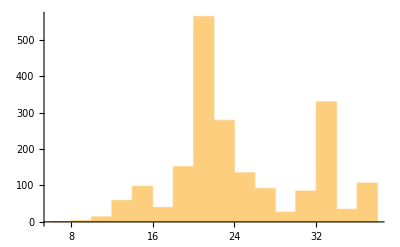

```mathematica
Histogram[Map[#[[1]]&,sllt36]]
```

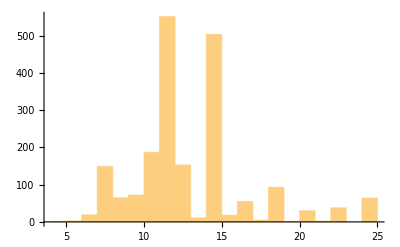

```mathematica
Histogram[Map[#[[2]]&,sllt36]]
```

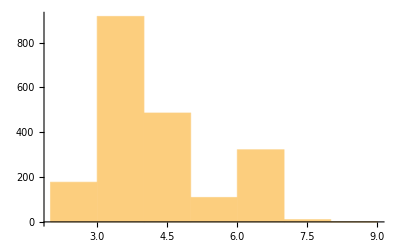

```mathematica
Histogram[Map[#[[3]]&,sllt36]]
```

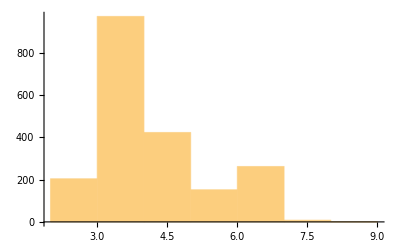

```mathematica
Histogram[Map[#[[4]]&,sllt36]]
```

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[9],goodgraph[GraphData[#]]&]]]
```

{14,15,15,15,16,16,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,20,20,20,20,20,21,21,23,23,23,23,24,24,24,24,25,26,27,27,27,27,28,29,30,32,33,34,35,36}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[18],goodgraph[GraphData[#]]&]]]
```

{27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,29,29,29,29,30,30,30,30,31,32,33,34,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,42,44,45,45,45,45,45,45,45,45,45,45,45,45,45,47,52,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,88,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,97,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,108,108,108,108,108,108,108,108,108,108,108,117,117,117,117,117,117,117,117,117,117,126,126,126,126,135,135,135,135,144,153}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[19],goodgraph[GraphData[#]]&]]]
```

{36,38,38,38,38,38,57,57,57,57,57,57,57,57,57,57,76,76,76,76,76,76,76,76,76,76,76,76,76,76,90,95,95,95,95,95,95,95,95,95,95,95,95,95,95,99,100,114,114,114,114,114,114,114,114,114,114,133,133,133,133,152,171}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[20],goodgraph[GraphData[#]]&]]]
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,33,35,35,36,36,38,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,44,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,55,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,110,118,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,140,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,160,160,160,160,160,160,160,170,170,170,170,180,190}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[21],goodgraph[GraphData[#]]&]]]
```

{35,35,42,42,56,70,84,105,105,105,118}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[22],goodgraph[GraphData[#]]&]]]
```

{33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,35,35,35,35,36,36,37,40,40,44,55,55,55,66,68,110,121,220}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[23],goodgraph[GraphData[#]]&]]]
```

{45,63,71,72,92}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[24],goodgraph[GraphData[#]]&]]]
```

{36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,40,42,46,48,48,48,48,48,48,56,60,60,60,60,65,68,72,72,72,72,72,72,72,72,72,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,85,88,96,96,96,96,96,96,96,96,96,96,96,108,108,108,108,108,108,108,108,108,108,108,108,120,120,120,120,120,120,120,120,120,120,120,132,132,132,132,132,132,132,132,132,132,132,132,132,144,144,144,144,144,144,144,144,144,144,144,144,144,144,148,148,156,156,156,156,156,156,156,156,156,156,156,168,168,168,168,168,168,168,168,168,168,168,168,180,180,180,180,180,180,180,180,180,192,192,192,192,192,192,192,204,204,204,204,204,216,264}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[25],goodgraph[GraphData[#]]&]]]
```

{45,45,50,50,50,50,55,60,69,72,80,94,100,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,160}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[26],goodgraph[GraphData[#]]&]]]
```

{39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,48,52,52,65,65,72,78,78,78,91,91,91,91,91,91,91,104,104,104,104,104,104,117,117,117,117,117,117,117,117,117,117,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,130,143,143,143,143,143,143,143,143,143,143,143,143,143,143,156,156,156,156,156,156,156,156,156,156,156,156,156,169,169,169,169,169,169,169,169,169,169,169,169,169,182,182,182,182,182,182,182,182,182,182,182,182,182,182,195,195,195,195,195,195,195,195,195,195,195,195,195,208,208,208,208,208,208,208,208,221,221,221,221,221,221,234,234,234,234,234,234,234,247,247,247,260,260,286,312}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[27],goodgraph[GraphData[#]]&]]]
```

{54,54,54,74,81,81,100,135,135,181,216}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[28],goodgraph[GraphData[#]]&]]]
```

{42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,45,48,48,49,56,56,56,70,70,70,81,84,84,84,84,84,84,98,112,112,126,126,126,126,126,126,126,140,140,140,154,168,168,168,168,168,168,168,168,168,182,182,182,182,182,182,182,182,190,196,196,196,196,196,196,196,196,210,210,210,210,210,224,238,238,238,252,252,252,252,252,252,266,280,294,294,294,294,294,308,308,322,336,364}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[29],goodgraph[GraphData[#]]&]]]
```

{145,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203,203}

```mathematica
Sort[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[30],goodgraph[GraphData[#]]&]]]
```

{45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,54,55,59,60,60,60,60,60,60,60,60,60,60,65,70,75,75,75,75,75,83,89,90,105,115,120,120,135,165,210,215,217,225,300,420}

```mathematica
Monitor[Table[Length[Map[Length[EdgeList[GraphData[#]]]&,Select[GraphData[mm],goodgraph[GraphData[#]]&]]],{mm,4,30}],mm]
```

{1,3,19,149,65,72,194,558,188,32,553,68,157,43,281,63,462,11,50,5,219,29,448,11,101,42,55}

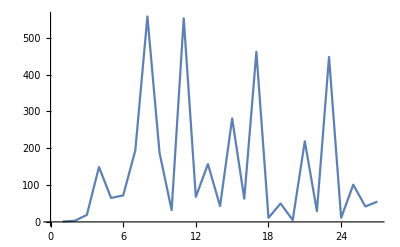

```mathematica
ListPlot[Out[96],Joined->True]
```

```mathematica
Select[GraphData[;;13],goodgraph[GraphData[#]]&]
```

{{6,114},{6,130},{6,148},{6,149},{7,344},{7,550},{7,551},{7,552},{7,553},{7,737},{7,738},{7,740},{7,763},{7,764},{7,765},{7,766},{7,767},{7,768},{7,770},{7,771},{7,772},{7,773},{7,839},{7,840},1234,{VertexTransitive,{12,32}},{VertexTransitive,{12,40}},{VertexTransitive,{12,45}},{VertexTransitive,{12,47}},{VertexTransitive,{12,48}},{VertexTransitive,{12,51}},{VertexTransitive,{12,54}},{VertexTransitive,{12,55}},{VertexTransitive,{12,60}},{VertexTransitive,{12,64}},{VertexTransitive,{12,65}},{VertexTransitive,{12,67}},WagnerGraph,{Wheel,5},{Wheel,6},{Wheel,7},{Wheel,8},{Wheel,9},{Wheel,10},{Wheel,11},{Wheel,12},{Wheel,13},{WhiteBishop,{5,5}}}
 |  |  |  |

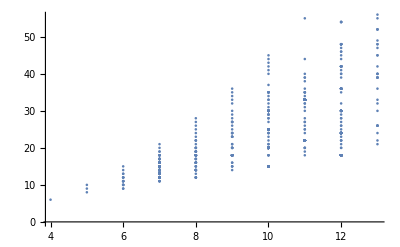

```mathematica
ListPlot[Map[{Length[VertexList[GraphData[#]]],Length[EdgeList[GraphData[#]]]}&,gg13]]
```

```mathematica
gg13=Out[5];
```

```mathematica
topyindex[Select[gg13,Length[EdgeList[GraphData[#]]]≤12&]]
```

graph_1_6,graph_2_6,graph_3_6,graph_4_7,graph_5_7,graph_6_7,graph_7_7,graph_8_7,graph_9_7,graph_10_7,graph_11_7,graph_12_6,graph_13_7,graph_14_6,graph_15_8,graph_16_8,graph_17_8,graph_18_6,graph_19_6,graph_20_7,graph_21_7,graph_22_7,graph_23_7,graph_24_7,graph_25_7,graph_26_7,graph_27_6,graph_28_6,graph_29_6,graph_30_5,graph_31_6,graph_32_8,graph_33_7,graph_34_6,graph_35_5,graph_36_6,graph_37_7,graph_38_7,graph_39_7,graph_40_4,graph_41_6,graph_42_8,graph_43_5,graph_44_6,graph_45_7,

```mathematica
Export["pytest.txt",topy[Select[gg13,Length[EdgeList[GraphData[#]]]≤12&]]]
```

pytest.txt

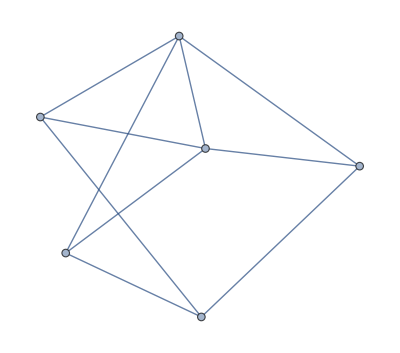
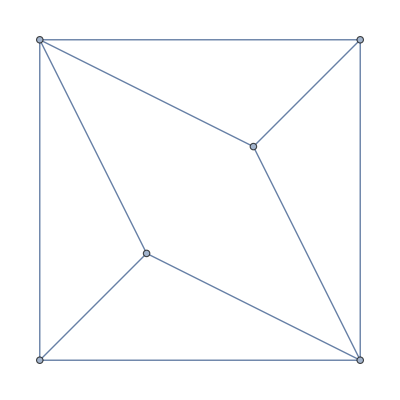
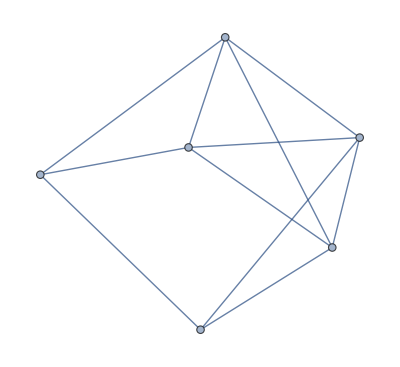
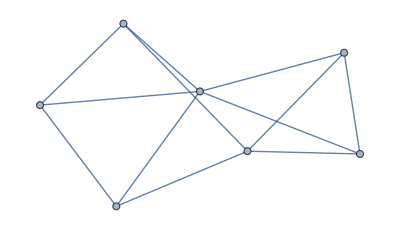
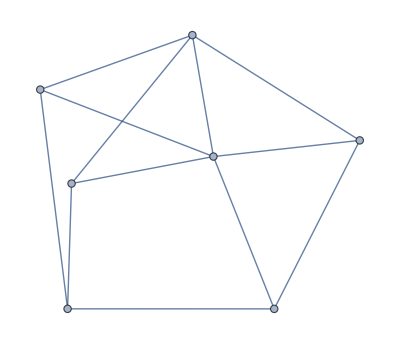
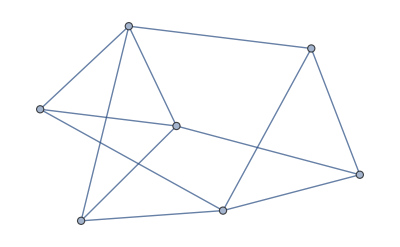
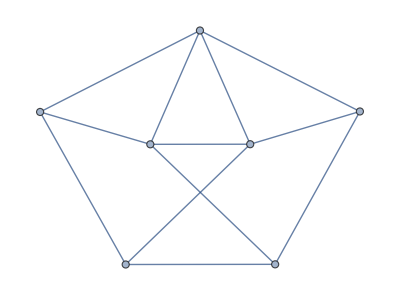
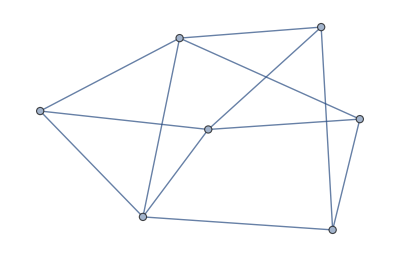

```mathematica
Map[GraphData,{{6,114},{6,130},{6,149},{7,550},{7,737},{7,763},{7,839},{7,888},{7,934},{7,956},{7,963},{"BiggestLittlePolygon",6},{"CompleteBipartite",{3,4}},{"Cone",{3,3}},{"Cubic",{8,2}},{"Cubic",{8,3}},"CubicalGraph",{"Fan",{2,4}},{"Fan",{3,3}},{"Harary",{3,7}},{"Heptahedral",2},{"Heptahedral",7},{"Heptahedral",8},{"Heptahedral",18},{"Heptahedral",21},{"Heptahedral",25},{"Hexahedral",3},{"Hexahedral",4},{"Hexahedral",5},{"JohnsonSkeleton",12},{"King",{2,3}},{"Matchstick",3},"MoserSpindle","OctahedralGraph","PentatopeGraph",{"Prism",3},"SelfDualGraph1","SelfDualGraph2","SelfDualGraph3","TetrahedralGraph","UtilityGraph","WagnerGraph",{"Wheel",5},{"Wheel",6},{"Wheel",7}}]
```

```mathematica
Map[Length[EdgeList[GraphData[#]]]&,gg13]
```

{{10,5},{13,33},{11,9},{12,26},{14,44},{15,54},{16,27},{17,13},{18,143},{19,9},{22,272},{23,7},{20,76},{24,33},{26,9},{32,6},{27,9},{30,41},{25,65},{35,11},{33,270},{44,3},{36,20},{48,9},{42,15},{54,4},{39,7},{52,3},{65,1},{40,7},{60,1},{21,8},{28,7},{45,4},{55,2},{66,1},{78,1},{29,5},{31,2},{38,1},{47,2},{56,1},{49,1},{34,3},{41,2},{9,3},{46,2},{6,1},{37,1},{43,1},{8,1}}

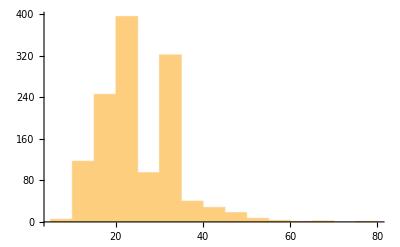

```mathematica
Tally[Out[8]]
Histogram[Out[8]]
```

```mathematica
Table[Total[Map[2^Length[EdgeList[GraphData[#]]]&,Select[GraphData[n],goodgraph[GraphData[#]]&]]]/(10^11*3600),{n,4,15}]
```

{1/5625000000000,7/1406250000000,19/70312500000,2351/87890625000,135743/87890625000,8287391/21972656250,236163066/1220703125,24448910168/244140625,763085157451736/3662109375,9224501688720073408/10986328125,76157493898745942145536/10986328125,1238053385310502343949244928/10986328125}

```mathematica
Map[N,%]
```

```mathematica
enum[{1.7777777777777777*^-13,4.977777777777778*^-12,2.702222222222222*^-10,2.6749155555555556*^-8,1.5444536888888888*^-6,0.00037716837262222224,0.1934647836672,100.142736048128,208373.12032815404,8.396346425999426*^8,6.932024333539187*^12,1.1269037036070706*^17}]
```

{{1,1.77778×10^-13},{2,4.97778×10^-12},{3,2.70222×10^-10},{4,2.67492×10^-8},{5,1.54445×10^-6},{6,0.000377168},{7,0.193465},{8,100.143},{9,208373.},{10,8.39635×10^8},{11,6.93202×10^12},{12,1.1269×10^17}}

```mathematica
ggasym[graph_]:=Block[{gg=goodgraph[graph]},Piecewise[{{(GroupOrder[GraphAutomorphismGroup[graph]]==1), gg}, {False, ¬gg}}]]
```

```mathematica
Monitor[Table[Total[Map[2^Length[EdgeList[GraphData[#]]]&,Select[GraphData[n],ggasym[GraphData[#]]&]]]/(10^11*3600),{n,4,30}],n]
```

{0,0,0,19/43945312500,16/10986328125,0,1408/3662109375,1136512/732421875,1576/10986328125,0,1055168/10986328125,0,512/10986328125,0,32768/10986328125,0,65536/10986328125,0,3407872/10986328125,281474976710656/10986328125,14680064/3662109375,17422457186352049329324783503386234322944/2197265625,13846124956092873676081324523257856/3662109375,0,0,784637716923335095479473677900958302012794430558004314112/1220703125,0}

```mathematica
Map[N,%]
```

{0.,0.,0.,4.32356×10^-10,1.45636×10^-9,0.,3.84478×10^-7,0.00155172,1.43451×10^-7,0.,0.0000960437,0.,4.66034×10^-8,0.,2.98262×10^-6,0.,5.96523×10^-6,0.,0.000310192,25620.5,0.00400864,7.92915×10^30,3.78092×10^24,0.,0.,6.42775×10^47,0.}

```mathematica
enum[Out[97]]
```

{{1,0.},{2,0.},{3,0.},{4,4.32356×10^-10},{5,1.45636×10^-9},{6,0.},{7,3.84478×10^-7},{8,0.00155172},{9,1.43451×10^-7},{10,0.},{11,0.0000960437},{12,0.},{13,4.66034×10^-8},{14,0.},{15,2.98262×10^-6},{16,0.},{17,5.96523×10^-6},{18,0.},{19,0.000310192},{20,25620.5},{21,0.00400864},{22,7.92915×10^30},{23,3.78092×10^24},{24,0.},{25,0.},{26,6.42775×10^47},{27,0.}}

```mathematica
enum[list_]:=Table[{i,list[[i]]},{i,1,Length[list]}]
```

```mathematica
StringReplace[StringReplace[ToString[Map[{#[[1]],#[[2]]}&,EdgeList[CompleteGraph[3]]]],{"{{"->"[{","}}"->"}]"}],{"{"->"(","}"->")"}]
```

[(1, 2), (1, 3), (2, 3)]

```mathematica
VertexCount
```

```mathematica
topy[namelist_]:=Block[{glist=Map[GraphData,namelist]},StringJoin[Table[StringJoin["graph_",ToString[i],"_",ToString[VertexCount[glist[[i]]]]," = Graph(",StringReplace[StringReplace[ToString[Map[{#[[1]],#[[2]]}&,EdgeList[glist[[i]]]]],{"{{"->"[{","}}"->"}]"}],{"{"->"(","}"->")"}],", directed = False)\n"],{i,1,Length[glist]}]]]
sizetopy[size_]:=Block[{namelist=Select[GraphData[size],goodgraph[GraphData[#]]&]},topy[namelist]]
```

```mathematica
topyindex[namelist_]:=Block[{glist=Map[GraphData,namelist]},StringJoin[Table[StringJoin["graph_",ToString[i],"_",ToString[VertexCount[glist[[i]]]],","],{i,1,Length[glist]}]]]
sizetopyindex[size_]:=Block[{namelist=Select[GraphData[size],goodgraph[GraphData[#]]&]},topyindex[namelist]]
```

```mathematica
sizetopyindex[5]
```

graph_1_5,graph_2_5,graph_3_5,

```mathematica
o5=sizetopy[5]
```

graph_1_5 = Graph([(1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (3, 4), (3, 5), (4, 5)], directed = False)
graph_2_5 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (3, 4), (3, 5), (4, 5)], directed = False)
graph_3_5 = Graph([(1, 2), (1, 4), (1, 5), (2, 3), (2, 5), (3, 4), (3, 5), (4, 5)], directed = False)

```mathematica
o6=sizetopy[6]
```

graph_1_6 = Graph([(1, 4), (1, 5), (1, 6), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6), (4, 6)], directed = False)
graph_2_6 = Graph([(1, 3), (1, 5), (1, 6), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (4, 5), (4, 6)], directed = False)
graph_3_6 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)
graph_4_6 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (2, 3), (2, 4), (2, 5), (3, 5), (3, 6), (4, 6), (5, 6)], directed = False)
graph_5_6 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (2, 3), (2, 5), (2, 6), (3, 4), (3, 6), (4, 5), (5, 6)], directed = False)
graph_6_6 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (2, 3), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)
graph_7_6 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (2, 3), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6)], directed = False)
graph_8_6 = Graph([(1, 2), (1, 5), (1, 6), (2, 3), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6), (4, 5), (4, 6)], directed = False)
graph_9_6 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (2, 3), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6)], directed = False)
graph_10_6 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (4, 6)], directed = False)
graph_11_6 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (4, 6), (5, 6)], directed = False)
graph_12_6 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)
graph_13_6 = Graph([(1, 2), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (4, 5), (5, 6)], directed = False)
graph_14_6 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 5), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)
graph_15_6 = Graph([(1, 2), (1, 3), (1, 4), (2, 3), (2, 5), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)
graph_16_6 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 4), (3, 5), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)
graph_17_6 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (2, 3), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)
graph_18_6 = Graph([(1, 4), (1, 5), (1, 6), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 6)], directed = False)
graph_19_6 = Graph([(1, 2), (1, 5), (1, 6), (2, 3), (2, 6), (3, 4), (3, 6), (4, 5), (4, 6), (5, 6)], directed = False)

```mathematica
o7=sizetopy[7]
```

graph_1_7 = Graph([(1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_2_7 = Graph([(1, 4), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_3_7 = Graph([(1, 4), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_4_7 = Graph([(1, 4), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_5_7 = Graph([(1, 4), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_6_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_7_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_8_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_9_7 = Graph([(1, 4), (1, 5), (1, 6), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_10_7 = Graph([(1, 4), (1, 5), (1, 6), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_11_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (6, 7)], directed = False)
graph_12_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_13_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_14_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_15_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (5, 7), (6, 7)], directed = False)
graph_16_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_17_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_18_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_19_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 7)], directed = False)
graph_20_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 7), (6, 7)], directed = False)
graph_21_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 7), (5, 7)], directed = False)
graph_22_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 7), (5, 7), (6, 7)], directed = False)
graph_23_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (5, 7), (6, 7)], directed = False)
graph_24_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (6, 7)], directed = False)
graph_25_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_26_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_27_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_28_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7)], directed = False)
graph_29_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 7)], directed = False)
graph_30_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 7), (6, 7)], directed = False)
graph_31_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 6), (5, 7)], directed = False)
graph_32_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_33_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7)], directed = False)
graph_34_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (6, 7)], directed = False)
graph_35_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_36_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_37_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_38_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_39_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (5, 7), (6, 7)], directed = False)
graph_40_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_41_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_42_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_43_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (4, 7), (5, 7)], directed = False)
graph_44_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 7)], directed = False)
graph_45_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 7), (5, 7)], directed = False)
graph_46_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (6, 7)], directed = False)
graph_47_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_48_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_49_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_50_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_51_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_52_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_53_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_54_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_55_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_56_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_57_7 = Graph([(1, 3), (1, 5), (1, 6), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_58_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7)], directed = False)
graph_59_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_60_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_61_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_62_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_63_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (6, 7)], directed = False)
graph_64_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_65_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_66_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_67_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (5, 7), (6, 7)], directed = False)
graph_68_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_69_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_70_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_71_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_72_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7), (6, 7)], directed = False)
graph_73_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (6, 7)], directed = False)
graph_74_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_75_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_76_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_77_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_78_7 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_79_7 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7), (6, 7)], directed = False)
graph_80_7 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_81_7 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_82_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7)], directed = False)
graph_83_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7)], directed = False)
graph_84_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_85_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_86_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_87_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7), (6, 7)], directed = False)
graph_88_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_89_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_90_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_91_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (5, 7), (6, 7)], directed = False)
graph_92_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_93_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_94_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_95_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_96_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_97_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (3, 7), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_98_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 6), (5, 7)], directed = False)
graph_99_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_100_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_101_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_102_7 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (2, 3), (2, 4), (2, 5), (2, 7), (3, 4), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7)], directed = False)
graph_103_7 = Graph([(1, 2), (1, 3), (1, 6), (1, 7), (2, 3), (2, 4), (2, 7), (3, 4), (3, 5), (4, 5), (4, 6), (5, 6), (5, 7), (6, 7)], directed = False)
graph_104_7 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_105_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7)], directed = False)
graph_106_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 7), (5, 7), (6, 7)], directed = False)
graph_107_7 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7)], directed = False)
graph_108_7 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7)], directed = False)
graph_109_7 = Graph([(1, 2), (1, 6), (1, 7), (2, 3), (2, 6), (2, 7), (3, 4), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_110_7 = Graph([(1, 2), (1, 5), (1, 6), (1, 7), (2, 3), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7)], directed = False)
graph_111_7 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7)], directed = False)
graph_112_7 = Graph([(1, 2), (1, 4), (1, 5), (1, 7), (2, 3), (2, 6), (3, 4), (3, 7), (4, 5), (5, 6), (6, 7)], directed = False)
graph_113_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7)], directed = False)
graph_114_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_115_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_116_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_117_7 = Graph([(1, 4), (1, 5), (1, 6), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 7)], directed = False)
graph_118_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 7)], directed = False)
graph_119_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 7), (5, 7), (6, 7)], directed = False)
graph_120_7 = Graph([(1, 4), (1, 5), (1, 6), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_121_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7), (6, 7)], directed = False)
graph_122_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_123_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_124_7 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_125_7 = Graph([(1, 4), (1, 5), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_126_7 = Graph([(1, 4), (1, 5), (1, 6), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 7), (6, 7)], directed = False)
graph_127_7 = Graph([(1, 4), (1, 5), (1, 6), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 7), (5, 7), (6, 7)], directed = False)
graph_128_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 7)], directed = False)
graph_129_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_130_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_131_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7)], directed = False)
graph_132_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_133_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_134_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_135_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_136_7 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 7)], directed = False)
graph_137_7 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 7)], directed = False)
graph_138_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_139_7 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7)], directed = False)
graph_140_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 7), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (4, 6), (4, 7), (5, 7)], directed = False)
graph_141_7 = Graph([(1, 2), (1, 5), (1, 7), (2, 3), (2, 6), (3, 4), (3, 6), (4, 5), (4, 6), (4, 7), (5, 7)], directed = False)
graph_142_7 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_143_7 = Graph([(1, 2), (1, 3), (1, 4), (1, 7), (2, 3), (2, 5), (2, 7), (3, 6), (3, 7), (4, 5), (4, 6), (5, 6)], directed = False)
graph_144_7 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 5), (3, 4), (3, 7), (4, 7), (5, 6), (6, 7)], directed = False)
graph_145_7 = Graph([(1, 4), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (3, 4), (3, 5), (3, 6), (5, 6), (5, 7), (6, 7)], directed = False)
graph_146_7 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 7), (5, 6), (6, 7)], directed = False)
graph_147_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 7), (6, 7)], directed = False)
graph_148_7 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)
graph_149_7 = Graph([(1, 2), (1, 6), (1, 7), (2, 3), (2, 7), (3, 4), (3, 7), (4, 5), (4, 7), (5, 6), (5, 7), (6, 7)], directed = False)

```mathematica
o8=sizetopy[8]
```

graph_1_8 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 7), (5, 8)], directed = False)
graph_2_8 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (1, 8), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 6), (4, 7), (4, 8), (5, 7), (6, 8)], directed = False)
graph_3_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 7), (1, 8), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 6), (4, 7), (4, 8), (5, 7), (5, 8)], directed = False)
graph_4_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (3, 8), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_5_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_6_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 7), (5, 8), (7, 8)], directed = False)
graph_7_8 = Graph([(1, 2), (1, 4), (1, 5), (1, 8), (2, 3), (2, 5), (2, 6), (3, 4), (3, 6), (3, 7), (4, 7), (4, 8), (5, 6), (5, 8), (6, 7), (7, 8)], directed = False)
graph_8_8 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 8), (2, 3), (2, 6), (2, 7), (3, 4), (3, 7), (3, 8), (4, 5), (4, 8), (5, 6), (6, 7), (7, 8)], directed = False)
graph_9_8 = Graph([(1, 2), (1, 3), (1, 5), (2, 4), (2, 6), (2, 8), (3, 4), (3, 5), (3, 7), (4, 8), (5, 6), (5, 7), (6, 8), (7, 8)], directed = False)
graph_10_8 = Graph([(1, 4), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 8), (4, 7), (4, 8), (5, 7), (6, 8), (7, 8)], directed = False)
graph_11_8 = Graph([(1, 2), (1, 3), (1, 5), (1, 7), (1, 8), (2, 3), (2, 4), (2, 6), (2, 8), (3, 4), (3, 5), (3, 7), (4, 5), (4, 6), (4, 8), (5, 6), (5, 7), (6, 7), (6, 8), (7, 8)], directed = False)
graph_12_8 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 8), (2, 3), (2, 5), (2, 6), (2, 7), (3, 4), (3, 6), (3, 7), (3, 8), (4, 5), (4, 7), (4, 8), (5, 6), (5, 8), (6, 7), (7, 8)], directed = False)
graph_13_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_14_8 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8)], directed = False)
graph_15_8 = Graph([(1, 5), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8)], directed = False)
graph_16_8 = Graph([(1, 5), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 8), (6, 8), (7, 8)], directed = False)
graph_17_8 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_18_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8)], directed = False)
graph_19_8 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8)], directed = False)
graph_20_8 = Graph([(1, 2), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 6), (2, 7), (2, 8), (3, 4), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8)], directed = False)
graph_21_8 = Graph([(1, 2), (1, 3), (1, 5), (2, 3), (2, 7), (3, 4), (4, 5), (4, 6), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_22_8 = Graph([(1, 2), (1, 5), (1, 8), (2, 3), (2, 6), (3, 4), (3, 7), (4, 5), (4, 6), (5, 8), (6, 7), (7, 8)], directed = False)
graph_23_8 = Graph([(1, 2), (1, 3), (1, 5), (2, 4), (2, 6), (3, 4), (3, 7), (4, 8), (5, 6), (5, 7), (6, 8), (7, 8)], directed = False)
graph_24_8 = Graph([(1, 2), (1, 7), (1, 8), (2, 3), (2, 7), (2, 8), (3, 4), (3, 7), (3, 8), (4, 5), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_25_8 = Graph([(1, 2), (1, 6), (1, 7), (1, 8), (2, 3), (2, 6), (2, 7), (2, 8), (3, 4), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8)], directed = False)
graph_26_8 = Graph([(1, 2), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8)], directed = False)
graph_27_8 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8)], directed = False)
graph_28_8 = Graph([(1, 5), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 7), (4, 8)], directed = False)
graph_29_8 = Graph([(1, 5), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 7), (4, 8)], directed = False)
graph_30_8 = Graph([(1, 5), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 6), (4, 7), (4, 8)], directed = False)
graph_31_8 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 8), (5, 7), (6, 8)], directed = False)
graph_32_8 = Graph([(1, 4), (1, 5), (1, 8), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 7), (6, 8)], directed = False)
graph_33_8 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (2, 8), (3, 5), (3, 6), (3, 8), (4, 6), (4, 7), (4, 8), (5, 7), (5, 8), (6, 8)], directed = False)
graph_34_8 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 5), (2, 7), (2, 8), (3, 5), (3, 6), (3, 8), (4, 6), (4, 7), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_35_8 = Graph([(1, 2), (1, 5), (1, 6), (2, 3), (2, 5), (2, 6), (2, 7), (3, 4), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 6), (6, 7), (7, 8)], directed = False)
graph_36_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 4), (3, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_37_8 = Graph([(1, 2), (1, 7), (1, 8), (2, 3), (2, 4), (3, 4), (3, 5), (4, 5), (5, 6), (6, 7), (6, 8), (7, 8)], directed = False)
graph_38_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (3, 6), (3, 7), (4, 6), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_39_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 5), (3, 7), (4, 7), (4, 8), (5, 6), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_40_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_41_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 7), (2, 3), (2, 4), (2, 6), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (4, 5), (4, 6), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_42_8 = Graph([(1, 4), (1, 5), (1, 6), (1, 8), (2, 4), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 7), (5, 8), (6, 8)], directed = False)
graph_43_8 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 4), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 7), (5, 8), (6, 8)], directed = False)
graph_44_8 = Graph([(1, 4), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 6)], directed = False)
graph_45_8 = Graph([(1, 4), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 7), (5, 8)], directed = False)
graph_46_8 = Graph([(1, 4), (1, 5), (1, 7), (2, 4), (2, 6), (2, 7), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 8), (6, 8)], directed = False)
graph_47_8 = Graph([(1, 2), (1, 3), (1, 4), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 8), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_48_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 7), (4, 6), (5, 7), (6, 7), (6, 8), (7, 8)], directed = False)
graph_49_8 = Graph([(1, 4), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 8), (3, 5), (3, 7), (3, 8), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_50_8 = Graph([(1, 4), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_51_8 = Graph([(1, 4), (1, 6), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (3, 5), (3, 6), (3, 8), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_52_8 = Graph([(1, 4), (1, 5), (1, 7), (1, 8), (2, 5), (2, 6), (2, 7), (2, 8), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_53_8 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 5), (2, 7), (2, 8), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_54_8 = Graph([(1, 4), (1, 5), (1, 7), (1, 8), (2, 4), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_55_8 = Graph([(1, 4), (1, 5), (1, 7), (1, 8), (2, 4), (2, 6), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 6), (4, 7), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_56_8 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 8), (7, 8)], directed = False)
graph_57_8 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (1, 8), (2, 4), (2, 6), (2, 7), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 8), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_58_8 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (1, 8), (2, 4), (2, 6), (2, 7), (2, 8), (3, 5), (3, 7), (3, 8), (4, 6), (4, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_59_8 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (2, 4), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 8), (4, 7), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_60_8 = Graph([(1, 3), (1, 5), (1, 6), (1, 7), (1, 8), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 7), (4, 6), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8)], directed = False)
graph_61_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_62_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_63_8 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (4, 5), (4, 6), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)
graph_64_8 = Graph([(1, 2), (1, 5), (1, 8), (2, 3), (2, 6), (3, 4), (3, 7), (4, 5), (4, 8), (5, 6), (6, 7), (7, 8)], directed = False)
graph_65_8 = Graph([(1, 2), (1, 7), (1, 8), (2, 3), (2, 8), (3, 4), (3, 8), (4, 5), (4, 8), (5, 6), (5, 8), (6, 7), (6, 8), (7, 8)], directed = False)

```mathematica
o9=sizetopy[9]
```

graph_1_9 = Graph([(1, 2), (1, 5), (1, 6), (1, 9), (2, 3), (2, 6), (2, 7), (3, 4), (3, 7), (3, 8), (4, 5), (4, 8), (4, 9), (5, 6), (5, 9), (6, 7), (7, 8), (8, 9)], directed = False)
graph_2_9 = Graph([(1, 2), (1, 4), (1, 7), (1, 9), (2, 3), (2, 5), (2, 8), (3, 4), (3, 6), (3, 9), (4, 5), (4, 7), (5, 6), (5, 8), (6, 7), (6, 9), (7, 8), (8, 9)], directed = False)
graph_3_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 9), (4, 5), (4, 6), (4, 7), (5, 6), (5, 7), (5, 8), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_4_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_5_9 = Graph([(1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9)], directed = False)
graph_6_9 = Graph([(1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9)], directed = False)
graph_7_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9)], directed = False)
graph_8_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 6), (2, 7), (2, 8), (2, 9), (3, 6), (3, 7), (3, 8), (3, 9), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9)], directed = False)
graph_9_9 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 6), (3, 7), (3, 8), (3, 9), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9)], directed = False)
graph_10_9 = Graph([(1, 2), (1, 3), (1, 5), (1, 6), (1, 8), (1, 9), (2, 3), (2, 4), (2, 6), (2, 7), (2, 9), (3, 4), (3, 5), (3, 7), (3, 8), (4, 5), (4, 6), (4, 8), (4, 9), (5, 6), (5, 7), (5, 9), (6, 7), (6, 8), (7, 8), (7, 9), (8, 9)], directed = False)
graph_11_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9)], directed = False)
graph_12_9 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9)], directed = False)
graph_13_9 = Graph([(1, 2), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9)], directed = False)
graph_14_9 = Graph([(1, 2), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 7), (2, 8), (2, 9), (3, 4), (3, 7), (3, 8), (3, 9), (4, 5), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9)], directed = False)
graph_15_9 = Graph([(1, 5), (1, 8), (1, 9), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 6), (3, 8), (3, 9), (4, 7), (4, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 9)], directed = False)
graph_16_9 = Graph([(1, 2), (1, 3), (1, 8), (2, 4), (2, 7), (2, 8), (3, 6), (3, 8), (3, 9), (4, 5), (4, 7), (5, 6), (5, 7), (5, 9), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_17_9 = Graph([(1, 2), (1, 8), (1, 9), (2, 3), (2, 8), (2, 9), (3, 4), (3, 8), (3, 9), (4, 5), (4, 8), (4, 9), (5, 6), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_18_9 = Graph([(1, 2), (1, 7), (1, 8), (1, 9), (2, 3), (2, 7), (2, 8), (2, 9), (3, 4), (3, 7), (3, 8), (3, 9), (4, 5), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9)], directed = False)
graph_19_9 = Graph([(1, 2), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9)], directed = False)
graph_20_9 = Graph([(1, 2), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9)], directed = False)
graph_21_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (2, 4), (2, 5), (2, 8), (3, 4), (3, 6), (3, 9), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (6, 7), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_22_9 = Graph([(1, 2), (1, 3), (1, 4), (2, 3), (2, 5), (3, 6), (4, 5), (4, 6), (4, 7), (5, 6), (5, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_23_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 7), (2, 5), (2, 7), (2, 8), (3, 4), (3, 8), (3, 9), (4, 5), (4, 6), (5, 6), (5, 8), (6, 7), (6, 9), (7, 9), (8, 9)], directed = False)
graph_24_9 = Graph([(1, 2), (1, 5), (1, 6), (1, 9), (2, 3), (2, 7), (3, 4), (3, 8), (4, 5), (4, 9), (5, 6), (6, 7), (7, 8), (8, 9)], directed = False)
graph_25_9 = Graph([(1, 2), (1, 3), (1, 5), (1, 6), (1, 8), (1, 9), (2, 3), (2, 4), (2, 7), (2, 9), (3, 4), (3, 5), (3, 8), (4, 5), (4, 6), (4, 9), (5, 6), (5, 7), (6, 7), (6, 8), (7, 8), (7, 9), (8, 9)], directed = False)
graph_26_9 = Graph([(1, 2), (1, 3), (1, 4), (2, 3), (2, 6), (2, 9), (3, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (6, 7), (6, 9), (8, 9)], directed = False)
graph_27_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 4), (2, 5), (2, 6), (3, 4), (3, 5), (3, 9), (4, 7), (5, 8), (6, 7), (6, 8), (7, 9), (8, 9)], directed = False)
graph_28_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 8), (3, 9), (4, 7), (4, 9), (5, 6), (5, 8), (6, 7), (6, 8), (6, 9), (7, 9), (8, 9)], directed = False)
graph_29_9 = Graph([(1, 2), (1, 3), (1, 4), (2, 3), (2, 8), (3, 9), (4, 5), (4, 6), (5, 6), (5, 7), (5, 8), (6, 7), (6, 9), (7, 8), (7, 9)], directed = False)
graph_30_9 = Graph([(1, 2), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (2, 6), (3, 5), (3, 6), (4, 5), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (8, 9)], directed = False)
graph_31_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (3, 4), (3, 6), (4, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_32_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (3, 6), (3, 7), (4, 6), (4, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_33_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 5), (3, 6), (3, 7), (4, 6), (4, 8), (5, 7), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_34_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 4), (3, 7), (4, 8), (5, 6), (5, 7), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_35_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 5), (3, 6), (4, 7), (4, 8), (5, 7), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_36_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 5), (3, 7), (4, 6), (4, 8), (5, 8), (5, 9), (6, 7), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_37_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 5), (3, 7), (4, 7), (4, 8), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 9), (8, 9)], directed = False)
graph_38_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 5), (3, 7), (4, 8), (4, 9), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_39_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 7), (3, 8), (4, 7), (4, 9), (5, 6), (5, 7), (5, 8), (6, 8), (6, 9), (7, 9), (8, 9)], directed = False)
graph_40_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 7), (3, 8), (4, 7), (4, 9), (5, 6), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_41_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 4), (2, 6), (3, 7), (3, 8), (4, 7), (4, 9), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (8, 9)], directed = False)
graph_42_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 6), (2, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_43_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (2, 3), (2, 6), (2, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 8), (5, 7), (5, 9), (6, 7), (6, 9), (7, 8), (8, 9)], directed = False)
graph_44_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 7), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 8), (3, 5), (3, 6), (3, 7), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (5, 6), (5, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_45_9 = Graph([(1, 5), (1, 7), (1, 8), (2, 5), (2, 8), (2, 9), (3, 6), (3, 7), (3, 8), (4, 6), (4, 8), (4, 9), (5, 6), (5, 7), (5, 9), (6, 7), (6, 9), (7, 9)], directed = False)
graph_46_9 = Graph([(1, 5), (1, 7), (1, 8), (2, 5), (2, 7), (2, 8), (3, 6), (3, 8), (3, 9), (4, 6), (4, 8), (4, 9), (5, 6), (5, 7), (5, 9), (6, 7), (6, 9), (7, 9)], directed = False)
graph_47_9 = Graph([(1, 4), (1, 6), (1, 8), (1, 9), (2, 5), (2, 7), (2, 8), (3, 6), (3, 7), (3, 8), (3, 9), (4, 7), (4, 8), (4, 9), (5, 7), (5, 9), (6, 8), (6, 9)], directed = False)
graph_48_9 = Graph([(1, 4), (1, 6), (1, 7), (2, 5), (2, 8), (2, 9), (3, 6), (3, 7), (3, 8), (3, 9), (4, 6), (4, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_49_9 = Graph([(1, 4), (1, 6), (1, 7), (2, 5), (2, 7), (2, 9), (3, 6), (3, 7), (3, 8), (3, 9), (4, 6), (4, 8), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_50_9 = Graph([(1, 4), (1, 6), (1, 7), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 7), (3, 8), (3, 9), (4, 6), (4, 8), (5, 7), (5, 8), (6, 9), (7, 9), (8, 9)], directed = False)
graph_51_9 = Graph([(1, 4), (1, 6), (1, 9), (2, 5), (2, 6), (2, 8), (3, 6), (3, 7), (3, 8), (3, 9), (4, 7), (4, 8), (5, 7), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_52_9 = Graph([(1, 4), (1, 6), (1, 8), (2, 5), (2, 6), (2, 8), (3, 6), (3, 7), (3, 8), (3, 9), (4, 7), (4, 9), (5, 7), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_53_9 = Graph([(1, 4), (1, 7), (1, 8), (1, 9), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 5), (3, 6), (3, 7), (3, 9), (4, 8), (4, 9), (5, 7), (6, 8), (6, 9)], directed = False)
graph_54_9 = Graph([(1, 4), (1, 5), (1, 7), (1, 8), (2, 5), (2, 6), (2, 9), (3, 6), (3, 7), (3, 8), (3, 9), (4, 7), (4, 8), (4, 9), (5, 8), (5, 9), (6, 8), (7, 9)], directed = False)
graph_55_9 = Graph([(1, 4), (1, 5), (1, 7), (1, 8), (2, 5), (2, 6), (2, 8), (3, 6), (3, 7), (3, 8), (3, 9), (4, 7), (4, 8), (4, 9), (5, 8), (5, 9), (6, 9), (7, 9)], directed = False)
graph_56_9 = Graph([(1, 4), (1, 5), (1, 7), (1, 8), (1, 9), (2, 5), (2, 6), (2, 8), (3, 6), (3, 7), (3, 9), (4, 7), (4, 8), (5, 9), (6, 7), (6, 8), (6, 9), (8, 9)], directed = False)
graph_57_9 = Graph([(1, 4), (1, 5), (1, 7), (1, 8), (1, 9), (2, 5), (2, 6), (2, 8), (3, 6), (3, 7), (3, 8), (4, 7), (4, 9), (5, 9), (6, 7), (6, 8), (6, 9), (8, 9)], directed = False)
graph_58_9 = Graph([(1, 4), (1, 5), (1, 7), (1, 9), (2, 5), (2, 6), (2, 7), (2, 8), (3, 6), (3, 8), (3, 9), (4, 7), (4, 8), (5, 8), (5, 9), (6, 7), (6, 9), (7, 9)], directed = False)
graph_59_9 = Graph([(1, 4), (1, 5), (1, 7), (1, 9), (2, 5), (2, 6), (2, 7), (2, 8), (3, 6), (3, 7), (3, 8), (4, 8), (4, 9), (5, 8), (5, 9), (6, 7), (6, 9), (7, 9)], directed = False)
graph_60_9 = Graph([(1, 4), (1, 5), (1, 7), (1, 9), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 6), (3, 7), (3, 8), (3, 9), (4, 7), (4, 9), (5, 8), (5, 9), (6, 8)], directed = False)
graph_61_9 = Graph([(1, 4), (1, 5), (1, 6), (1, 8), (1, 9), (2, 5), (2, 6), (2, 7), (2, 9), (3, 6), (3, 7), (3, 9), (4, 7), (4, 8), (4, 9), (5, 8), (6, 8), (7, 9)], directed = False)
graph_62_9 = Graph([(1, 4), (1, 5), (1, 6), (1, 8), (2, 5), (2, 6), (2, 7), (2, 9), (3, 6), (3, 7), (3, 8), (4, 7), (4, 8), (4, 9), (5, 9), (6, 8), (7, 9), (8, 9)], directed = False)
graph_63_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (3, 4), (3, 5), (3, 8), (3, 9), (4, 6), (4, 8), (4, 9), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_64_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (2, 3), (2, 4), (2, 5), (2, 6), (2, 8), (3, 4), (3, 5), (3, 6), (3, 9), (4, 7), (4, 8), (4, 9), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)
graph_65_9 = Graph([(1, 3), (1, 4), (1, 6), (1, 7), (1, 9), (2, 4), (2, 5), (2, 6), (2, 8), (2, 9), (3, 5), (3, 7), (3, 8), (4, 6), (4, 8), (5, 7), (5, 8), (5, 9), (6, 9), (7, 9)], directed = False)
graph_66_9 = Graph([(1, 2), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 9), (6, 7), (7, 8), (8, 9)], directed = False)
graph_67_9 = Graph([(1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9)], directed = False)
graph_68_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_69_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_70_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_71_9 = Graph([(1, 2), (1, 3), (1, 4), (1, 5), (1, 6), (1, 7), (1, 8), (1, 9), (2, 3), (2, 4), (2, 5), (2, 6), (2, 7), (2, 8), (2, 9), (3, 4), (3, 5), (3, 6), (3, 7), (3, 8), (3, 9), (4, 5), (4, 6), (4, 7), (4, 8), (4, 9), (5, 6), (5, 7), (5, 8), (5, 9), (6, 7), (6, 8), (6, 9), (7, 8), (7, 9)], directed = False)
graph_72_9 = Graph([(1, 2), (1, 8), (1, 9), (2, 3), (2, 9), (3, 4), (3, 9), (4, 5), (4, 9), (5, 6), (5, 9), (6, 7), (6, 9), (7, 8), (7, 9), (8, 9)], directed = False)

```mathematica
names=StringReplace[StringJoin["namelist = [",Table[sizetopyindex[i],{i,5,9}],"]\n\n"],{",]"->"]"}]
```

namelist = [graph_1_5,graph_2_5,graph_3_5,graph_1_6,graph_2_6,graph_3_6,graph_4_6,graph_5_6,graph_6_6,graph_7_6,graph_8_6,graph_9_6,graph_10_6,graph_11_6,graph_12_6,graph_13_6,graph_14_6,graph_15_6,graph_16_6,graph_17_6,graph_18_6,graph_19_6,graph_1_7,graph_2_7,graph_3_7,graph_4_7,graph_5_7,graph_6_7,graph_7_7,graph_8_7,graph_9_7,graph_10_7,graph_11_7,graph_12_7,graph_13_7,graph_14_7,graph_15_7,graph_16_7,graph_17_7,graph_18_7,graph_19_7,graph_20_7,graph_21_7,graph_22_7,graph_23_7,graph_24_7,graph_25_7,graph_26_7,graph_27_7,graph_28_7,graph_29_7,graph_30_7,graph_31_7,graph_32_7,graph_33_7,graph_34_7,graph_35_7,graph_36_7,graph_37_7,graph_38_7,graph_39_7,graph_40_7,graph_41_7,graph_42_7,graph_43_7,graph_44_7,graph_45_7,graph_46_7,graph_47_7,graph_48_7,graph_49_7,graph_50_7,graph_51_7,graph_52_7,graph_53_7,graph_54_7,graph_55_7,graph_56_7,graph_57_7,graph_58_7,graph_59_7,graph_60_7,graph_61_7,graph_62_7,graph_63_7,graph_64_7,graph_65_7,graph_66_7,graph_67_7,graph_68_7,graph_69_7,graph_70_7,graph_71_7,graph_72_7,graph_73_7,graph_74_7,graph_75_7,graph_76_7,graph_77_7,graph_78_7,graph_79_7,graph_80_7,graph_81_7,graph_82_7,graph_83_7,graph_84_7,graph_85_7,graph_86_7,graph_87_7,graph_88_7,graph_89_7,graph_90_7,graph_91_7,graph_92_7,graph_93_7,graph_94_7,graph_95_7,graph_96_7,graph_97_7,graph_98_7,graph_99_7,graph_100_7,graph_101_7,graph_102_7,graph_103_7,graph_104_7,graph_105_7,graph_106_7,graph_107_7,graph_108_7,graph_109_7,graph_110_7,graph_111_7,graph_112_7,graph_113_7,graph_114_7,graph_115_7,graph_116_7,graph_117_7,graph_118_7,graph_119_7,graph_120_7,graph_121_7,graph_122_7,graph_123_7,graph_124_7,graph_125_7,graph_126_7,graph_127_7,graph_128_7,graph_129_7,graph_130_7,graph_131_7,graph_132_7,graph_133_7,graph_134_7,graph_135_7,graph_136_7,graph_137_7,graph_138_7,graph_139_7,graph_140_7,graph_141_7,graph_142_7,graph_143_7,graph_144_7,graph_145_7,graph_146_7,graph_147_7,graph_148_7,graph_149_7,graph_1_8,graph_2_8,graph_3_8,graph_4_8,graph_5_8,graph_6_8,graph_7_8,graph_8_8,graph_9_8,graph_10_8,graph_11_8,graph_12_8,graph_13_8,graph_14_8,graph_15_8,graph_16_8,graph_17_8,graph_18_8,graph_19_8,graph_20_8,graph_21_8,graph_22_8,graph_23_8,graph_24_8,graph_25_8,graph_26_8,graph_27_8,graph_28_8,graph_29_8,graph_30_8,graph_31_8,graph_32_8,graph_33_8,graph_34_8,graph_35_8,graph_36_8,graph_37_8,graph_38_8,graph_39_8,graph_40_8,graph_41_8,graph_42_8,graph_43_8,graph_44_8,graph_45_8,graph_46_8,graph_47_8,graph_48_8,graph_49_8,graph_50_8,graph_51_8,graph_52_8,graph_53_8,graph_54_8,graph_55_8,graph_56_8,graph_57_8,graph_58_8,graph_59_8,graph_60_8,graph_61_8,graph_62_8,graph_63_8,graph_64_8,graph_65_8,graph_1_9,graph_2_9,graph_3_9,graph_4_9,graph_5_9,graph_6_9,graph_7_9,graph_8_9,graph_9_9,graph_10_9,graph_11_9,graph_12_9,graph_13_9,graph_14_9,graph_15_9,graph_16_9,graph_17_9,graph_18_9,graph_19_9,graph_20_9,graph_21_9,graph_22_9,graph_23_9,graph_24_9,graph_25_9,graph_26_9,graph_27_9,graph_28_9,graph_29_9,graph_30_9,graph_31_9,graph_32_9,graph_33_9,graph_34_9,graph_35_9,graph_36_9,graph_37_9,graph_38_9,graph_39_9,graph_40_9,graph_41_9,graph_42_9,graph_43_9,graph_44_9,graph_45_9,graph_46_9,graph_47_9,graph_48_9,graph_49_9,graph_50_9,graph_51_9,graph_52_9,graph_53_9,graph_54_9,graph_55_9,graph_56_9,graph_57_9,graph_58_9,graph_59_9,graph_60_9,graph_61_9,graph_62_9,graph_63_9,graph_64_9,graph_65_9,graph_66_9,graph_67_9,graph_68_9,graph_69_9,graph_70_9,graph_71_9,graph_72_9]

```mathematica
Export["pygraphs.txt",StringJoin[names,o5,o6,o7,o8,o9],"TEXT"]
```

pygraphs.txt

```mathematica
Flatten[Table[GraphData[i],{i,5,6}],1]
```

{{5,2},{5,3},{5,4},{5,6},{5,7},{5,8},{5,9},{5,10},{5,14},{5,15},{5,20},{5,24},{5,31},BannerGraph,BullGraph,ButterflyGraph,{CompleteBipartite,{2,3}},CricketGraph,{Cycle,5},DartGraph,{Empty,5},{Fan,{3,2}},ForkGraph,GemGraph,HouseGraph,HouseXGraph,{JohnsonSkeleton,12},KiteGraph,{Lollipop,{4,1}},{Path,5},PentatopeGraph,{Star,5},{Tadpole,{3,2}},{Wheel,5},{6,2},{6,3},{6,4},{6,5},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,16},{6,19},{6,21},{6,22},{6,23},{6,24},{6,25},{6,28},{6,29},{6,30},{6,31},{6,32},{6,33},{6,38},{6,39},{6,40},{6,41},{6,42},{6,44},{6,45},{6,46},{6,47},{6,48},{6,49},{6,51},{6,53},{6,55},{6,57},{6,58},{6,59},{6,60},{6,61},{6,62},{6,65},{6,66},{6,67},{6,69},{6,70},{6,71},{6,72},{6,73},{6,74},{6,75},{6,76},{6,77},{6,78},{6,79},{6,80},{6,81},{6,82},{6,83},{6,84},{6,86},{6,88},{6,90},{6,92},{6,95},{6,96},{6,97},{6,98},{6,99},{6,100},{6,101},{6,102},{6,103},{6,104},{6,105},{6,106},{6,108},{6,109},{6,110},{6,111},{6,112},{6,114},{6,118},{6,120},{6,122},{6,123},{6,124},{6,125},{6,127},{6,128},{6,129},{6,130},{6,132},{6,133},{6,135},{6,136},{6,137},{6,138},{6,139},{6,140},{6,141},{6,144},{6,148},{6,149},{6,150},AGraph,AntennaGraph,{Barbell,3},{BiggestLittlePolygon,6},{BlackBishop,{3,4}},{Complete,6},{CompleteBipartite,{2,4}},{Cone,{3,3}},CrossGraph,{Cycle,6},DominoGraph,EGraph,{Empty,6},{Fan,{1,5}},{Fan,{2,4}},{Fan,{3,3}},{Fan,{4,2}},FishGraph,{HamiltonLaceable,{6,1}},{Hexahedral,3},{Hexahedral,4},{Hexahedral,5},HGraph,{King,{2,3}},{Knight,{2,3}},{LadderRung,3},{Lollipop,{4,2}},{Lollipop,{5,1}},MothGraph,NetGraph,OctahedralGraph,{Pan,5},{Path,6},{Polyiamond,{4,1}},{Prism,3},{Queen,{2,3}},RGraph,{Star,6},{Tadpole,{3,3}},{Tadpole,{4,2}},{Tree,{6,2}},{TriangularGrid,2},{TriangularHoneycombRook,3},{Turan,{6,5}},TwoP3,TwoTriangles,UtilityGraph,{Wheel,6}}

```mathematica
Map[GroupOrder[GraphAutomorphismGroup[GraphData[#]]]&,Select[Flatten[Table[GraphData[i],{i,5,12}],1],goodgraph[GraphData[#]]&]]
```

{12,120,8,12,16,12,8,4,720,36,4,12,2,2,4,16,48,12,16,48,72,10,48,4,4,8,8,2,4,4,4,2,4,2,2,4,4,8,8,24,2,1,2,2,2,2,1,1,4,4,2,8,2,4,4,4,2,2,4,4,4,4,4,12,8,24,12,36,12,24,144,4,8,4,4,4,24,24,4,4,2,4,2,4,4,2,2,4,4,16,16,48,8,2,8,2,2,4,36,2,2,2,20,4,2,2,12,2,1,2,2,4,4,4,4,12,48,8,12,4,12,8,16,6,14,5040,144,72,144,48,4,12,48,4,2,2,2,2,4,2,4,1,2,1,1,4,2,1,2,2,2,2,2,1,4,1,2,2,2,6,20,4,8,48,6,1,6,48,48,240,12,48,4,4,48,12,48,16,2,8,8,16,128,40320,720,1152,144,144,720,192,60,4,12,48,4,12,48,240,12,16,72,12,8,4,8,32,48,16,12,4,16,8,4,2,32,2,8,384,24,1,1,2,4,4,24,2,4,2,2,2,12,96,192,1440,16,14,18,18,18,362880,4320,2880,720,1152,288,1296,4320,960,240,72,3,6,4,12,48,240,12,12,72,2,4,6,8,8,6,8,16,32,4,8,12,2,2,4,2,8,8,16,12,16,8,32,4,32,2,4,8,8,2,2,2,2,2,2,2,2,2,2,80,72,2,80,288,384,288,960,10080,16,20,2,320,20,20,20,320,240,20,3840,3628800,30240,17280,28800,2880,1440,2304,1728,30240,5760,1200,288,84,240,16,4,8,16,2,4,4,8,12,6,6,2,48,4,8,4,12,48,240,6,16,16,4,6,4,64,20,120,20,144,64,8,4,8,8,12,48,4,4,16,2,8,2,16,2,8,2,4,1,4,4,2,2,2,2,4,1,1,2,2,32,2,2,2,4,1,4,2,8,4,4,4,4,4,2,2,16,2,16,16,2,10,4,8,4,8,4,32,8,2,8,16,8,4,8,16,4,4,48,4,12,2,2,2,2,2,2,1,1,4,4,16,2,2,4,2,16,4,2,1,4,1,2,16,8,2,4,2,2,2,2,2,8,4,144,16,4,4,4,10,64,96,576,84,1728,16,48,4,32,6,4,4,2,4,8,8,2,8,16,6,96,200,120,12,576,768,1152,5760,80640,18,22,22,22,22,22,39916800,241920,120960,86400,28800,5760,8640,6912,241920,40320,7200,1440,336,96,12,48,240,12,10,12,10,10,4,2,120,48,24,16,16,32,8,8,2,4,8,4,2,16,2,8,4,8,32,8,4,64,4,12,4,8,4,2,4,2,8,4,2,2,2,8,4,2,4,2,2,4,4,4,8,16,24,24,8,12,6,12,2,2,1,4,4,2,4,144,4,4,8,2,2,1,4,16,2,2,2,8,16,2,4,2,2,1,4,2,2,1,1,1,2,2,1,1,2,2,1,2,4,1,2,1,2,2,2,1,1,1,1,1,1,1,2,2,1,8,1,1,1,1,2,1,1,1,4,1,4,1,1,4,2,1,4,1,1,1,4,8,1,1,2,2,2,4,8,2,1,2,2,2,2,8,2,8,8,4,1,1,2,2,2,4,4,2,1,2,2,2,2,1,1,1,1,4,2,1,2,2,4,2,4,2,2,1,1,4,2,4,1,1,2,12,4,4,2,1,1,2,1,1,1,4,4,2,2,1,2,2,2,8,2,1,1,2,2,1,2,2,8,2,1,1,1,2,4,4,2,1,2,4,2,2,4,32,4,1,8,4,4,4,16,4,2,1,1,4,2,2,4,2,1,6,4,4,4,2,2,4,2,2,4,2,2,2,4,2,12,6,48,144,8,4,8,16,4,2,4,8,32,64,48,4,8,8,8,16,8,4,4,4,2,2,2,2,4,4,4,4,8,2,2,8,4,4,32,32,8,2,8,8,16,16,288,4,8,16,24,5760,4,4,8,1,1,4,12,4,2,2,4,24,8,2,2,2,12,4,6,2,2,1,2,1,2,2,2,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,2,4,4,1,1,1,1,1,2,2,2,8,2,1,1,4,4,2,4,2,2,1,4,1,1,4,2,2,1,2,1,1,1,4,2,2,1,2,1,1,1,2,1,4,4,2,2,2,1,2,1,1,4,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,2,2,4,2,2,2,8,4,4,2,1,1,1,4,4,1,2,8,1,8,1,2,2,1,4,4,4,2,2,8,4,4,1,4,2,4,2,2,2,1,2,2,1,2,1,2,2,1,12,4,1,1,4,2,1,2,2,2,1,2,2,2,2,4,16,1,4,48,8,4,16,4,4,2,6,4,12,1,4,6,2,2,2,1,2,1,2,2,2,2,4,4,2,2,4,2,4,8,24,2,4,2,12,2,4,112,20,24,4,8,24,24,768,48,48,24,24,144,24,24,24,48,24,768,768,48,144,24,24,24,48,10368,24,4608,48,768,24,3072,288,46080,479001600,2177280,967680,604800,1036800,31104,57600,17280,82944,2177280,322560,50400,8640,1680,384,108,1440,16,4,8,16,32,8,4,2,8,2,48,8,8,4,8,8,8,4,4,4,8,16,16,2,2,1,2,4,4,2,2,2,2,2,1,4,8,12,2,4,2,2,2,4,1,4,2,2,2,2,1,4,4,4,36,64,16,12,4,4,2,4,8,2,16,2,8,2,4,8,4,16,18,8,48,12,48,240,48,1,12,16,120,8,20,12,4,4,128,4,1440,24,2,24,2,8,64,1,4,16,4,8,1,1,4,24,48,144,4,4,6,4,20,36,8,48,12,128,288,24,4,48,12,12,96,120,12,12,96,48,48,24,144,24,24,48,22,32}

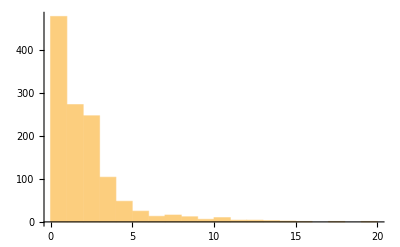

```mathematica
Histogram[Map[N[Log[#]]&,Out[65]]]
```

```mathematica
Total[Map[Boole[#==1]&,Out[58]]]/Length[Out[65]]
N[%]
```

1/96

0.0104167

```mathematica
Map[Length[EdgeList[GraphData[#]]]&,Select[Flatten[Table[GraphData[i],{i,5,9}],1],goodgraph[GraphData[#]]&]]
```

{9,10,8,10,10,13,11,12,15,12,11,11,10,11,12,11,12,9,13,14,9,10,13,12,13,13,14,12,13,14,12,13,13,13,14,15,14,14,15,16,12,13,13,14,14,14,14,15,16,12,13,14,14,15,13,14,14,15,16,15,15,15,16,17,13,13,14,15,16,17,18,12,13,13,13,14,14,15,12,12,13,14,14,15,14,14,15,16,15,15,16,17,16,15,15,15,16,17,18,14,14,15,16,13,13,14,15,16,15,15,16,17,16,16,17,18,19,17,16,16,17,18,17,15,14,21,12,15,15,16,14,15,14,11,11,13,13,14,11,12,13,13,13,13,14,15,14,12,13,12,13,14,12,13,14,14,15,13,14,15,15,13,11,14,12,12,12,19,18,20,12,19,19,19,22,22,23,16,16,14,14,20,20,28,15,16,19,21,18,20,20,12,12,12,17,19,19,17,13,14,15,15,14,17,18,16,16,12,16,16,16,22,17,18,14,14,14,24,18,18,18,18,18,18,18,18,18,18,18,18,18,25,26,27,12,14,18,18,27,36,18,20,23,24,26,27,21,24,25,24,18,18,20,23,24,23,21,15,18,14,23,15,16,20,15,20,18,18,18,18,18,18,18,18,18,18,18,18,18,28,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,27,27,20,29,30,32,33,34,35,16}

```mathematica
{18,18,27,36,18,20,23,24,26,27,21,24,25,24,18,18,20,23,24,23,21,15,18,14,23,15,16,20,15,20,18,18,18,18,18,18,18,18,18,18,18,18,18,28,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,27,27,20,29,30,32,33,34,35,16}-18
```

```mathematica
Table[{i,N[8000/10^9*Total[Map[2^#&,Select[{9,10,8,10,10,13,11,12,15,12,11,11,10,11,12,11,12,9,13,14,9,10,13,12,13,13,14,12,13,14,12,13,13,13,14,15,14,14,15,16,12,13,13,14,14,14,14,15,16,12,13,14,14,15,13,14,14,15,16,15,15,15,16,17,13,13,14,15,16,17,18,12,13,13,13,14,14,15,12,12,13,14,14,15,14,14,15,16,15,15,16,17,16,15,15,15,16,17,18,14,14,15,16,13,13,14,15,16,15,15,16,17,16,16,17,18,19,17,16,16,17,18,17,15,14,21,12,15,15,16,14,15,14,11,11,13,13,14,11,12,13,13,13,13,14,15,14,12,13,12,13,14,12,13,14,14,15,13,14,15,15,13,11,14,12,12,12,19,18,20,12,19,19,19,22,22,23,16,16,14,14,20,20,28,15,16,19,21,18,20,20,12,12,12,17,19,19,17,13,14,15,15,14,17,18,16,16,12,16,16,16,22,17,18,14,14,14,24,18,18,18,18,18,18,18,18,18,18,18,18,18,25,26,27,12,14,18,18,27,36,18,20,23,24,26,27,21,24,25,24,18,18,20,23,24,23,21,15,18,14,23,15,16,20,15,20,18,18,18,18,18,18,18,18,18,18,18,18,18,28,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,27,27,20,29,30,32,33,34,35,16}-i,#>0&]]]]},{i,1,30}]//Column
```

{1,545385.}
{2,272693.}
{3,136346.}
{4,68173.2}
{5,34086.6}
{6,17043.3}
{7,8521.65}
{8,4260.82}
{9,2130.41}
{10,1065.21}
{11,532.603}
{12,266.301}
{13,133.15}
{14,66.5748}
{15,33.2871}
{16,16.6433}
{17,8.32157}
{18,4.16032}
{19,2.0801}
{20,1.03997}
{21,0.519952}
{22,0.259952}
{23,0.129936}
{24,0.064928}
{25,0.032448}
{26,0.016208}
{27,0.008064}
{28,0.004016}
{29,0.002}
{30,0.000992}

```mathematica
2^18
```

262144

```mathematica
Select[GraphData[6],goodgraph[GraphData[#]]&]
```

{{6,114},{6,130},{6,148},{6,149},{BiggestLittlePolygon,6},{Complete,6},{Cone,{3,3}},{Fan,{2,4}},{Fan,{3,3}},{Hexahedral,3},{Hexahedral,4},{Hexahedral,5},{King,{2,3}},OctahedralGraph,{Prism,3},{Queen,{2,3}},{Turan,{6,5}},UtilityGraph,{Wheel,6}}

```mathematica
Select[GraphData[7],goodgraph[GraphData[#]]&]
```

{{7,344},{7,550},{7,551},{7,552},{7,553},{7,737},{7,738},{7,740},{7,763},{7,764},{7,765},{7,766},{7,767},{7,768},{7,770},{7,771},{7,772},{7,773},{7,839},{7,840},{7,841},{7,842},{7,843},{7,844},{7,845},{7,846},{7,847},{7,888},{7,889},{7,890},{7,892},{7,893},{7,894},{7,895},{7,896},{7,897},{7,898},{7,899},{7,901},{7,902},{7,903},{7,904},{7,905},{7,906},{7,907},{7,910},{7,912},{7,914},{7,915},{7,934},{7,935},{7,949},{7,952},{7,953},{7,954},{7,955},{7,956},{7,963},{7,964},{7,965},{7,967},{7,968},{7,986},{7,987},{7,988},{7,989},{7,990},{7,991},{7,992},{7,993},{7,1001},{7,1002},{7,1003},{7,1004},{7,1005},{7,1006},{7,1007},{7,1008},{7,1009},{7,1013},{7,1015},{7,1017},{7,1018},{7,1019},{7,1020},{7,1023},{7,1025},{7,1026},{7,1027},{7,1028},{7,1029},{7,1030},{7,1031},{7,1032},{7,1033},{7,1034},{7,1035},{7,1037},{7,1038},{7,1039},{7,1040},{Apollonian,2},{Circulant,{7,{1,2}}},{Complete,7},{CompleteBipartite,{3,4}},{CompleteTripartite,{1,3,3}},{Cone,{3,4}},{Cone,{4,3}},{Fan,{2,5}},{Fan,{3,4}},{Fan,{4,3}},{Harary,{3,7}},{Heptahedral,2},{Heptahedral,4},{Heptahedral,5},{Heptahedral,6},{Heptahedral,7},{Heptahedral,8},{Heptahedral,9},{Heptahedral,10},{Heptahedral,11},{Heptahedral,12},{Heptahedral,13},{Heptahedral,15},{Heptahedral,16},{Heptahedral,18},{Heptahedral,20},{Heptahedral,21},{Heptahedral,22},{Heptahedral,23},{Heptahedral,25},{Heptahedral,26},{Heptahedral,27},{Heptahedral,28},{Heptahedral,29},{Heptahedral,30},{Heptahedral,31},{Heptahedral,34},{JohnsonSkeleton,13},{JohnsonSkeleton,49},MoserSpindle,{Quartic,{7,1}},SelfDualGraph1,SelfDualGraph2,SelfDualGraph3,{TorusGrid,{3,4}},{Turan,{7,4}},{Turan,{7,6}},{Wheel,7}}

```mathematica
Select[GraphData[8],goodgraph[GraphData[#]]&]
```

{{8,11690},{8,12276},{8,12291},{8,12332},{8,12334},{8,12339},{Antiprism,4},{BiggestLittlePolygon,8},BislitCube,{BlackBishop,{4,4}},{Circulant,{8,{1,2,4}}},{Circulant,{8,{1,3,4}}},{Complete,8},{CompleteBipartite,{3,5}},{CompleteBipartite,{4,4}},{CompleteTripartite,{1,3,4}},{CompleteTripartite,{2,3,3}},{Cone,{3,5}},{Cone,{4,4}},{Cone,{5,3}},{Cubic,{8,2}},{Cubic,{8,3}},CubicalGraph,{Fan,{2,6}},{Fan,{3,5}},{Fan,{4,4}},{Fan,{5,3}},{HamiltonLaceable,{8,7}},{HamiltonLaceable,{8,8}},{HamiltonLaceable,{8,11}},{JohnsonSkeleton,14},{JohnsonSkeleton,26},{JohnsonSkeleton,50},{JohnsonSkeleton,84},{King,{2,4}},{Lattice,{2,4}},{Matchstick,3},{Quartic,{8,1}},{Quartic,{8,4}},{Quartic,{8,5}},{Queen,{2,4}},RoyleGraph1,RoyleGraph2,{SelfComplementary,{8,5}},{SelfComplementary,{8,6}},{SelfComplementary,{8,10}},SixteenCellGraph,TriakisTetrahedralGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,7}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}},{Turan,{8,5}},{Turan,{8,6}},{Turan,{8,7}},WagnerGraph,{Wheel,8}}

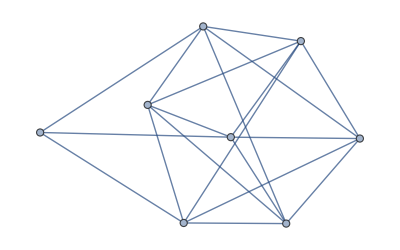
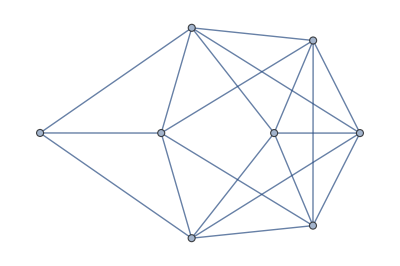
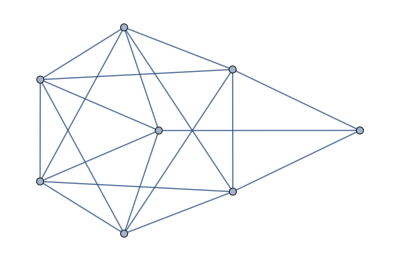
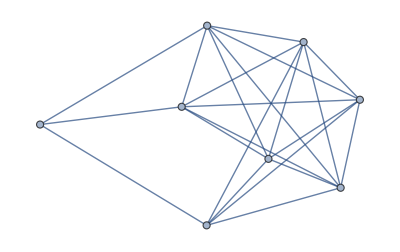
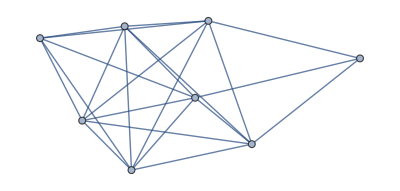
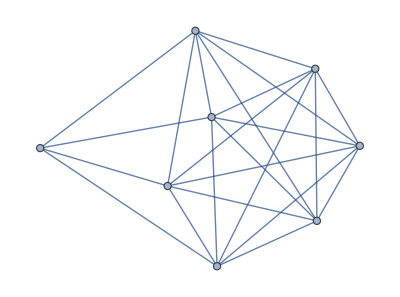
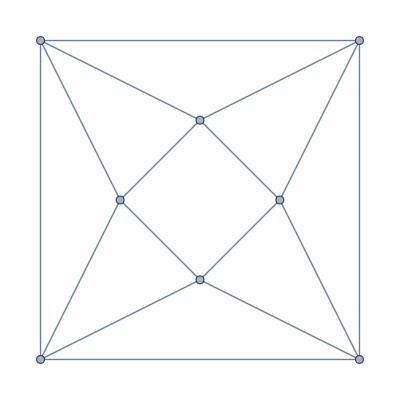
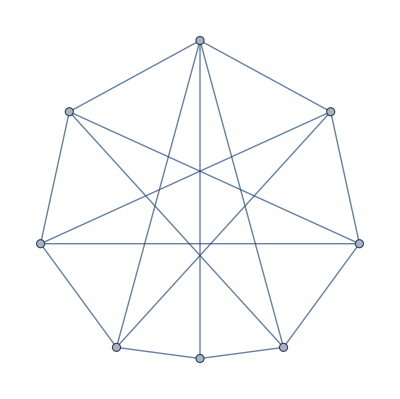
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[GraphData,Out[11]]
```

```mathematica
Length[EdgeList[CompleteGraph[8]]]
```

28

```mathematica
Length[Out[11]]+Length[Out[10]]+Length[Out[9]]+Length[Out[8]]
```

236